## Self-tuning kinetic gravity braiding: Cosmological dynamics, shift symmetry, and the tadpole

This notebook serves as a supplement to the paper “Self-tuning kinetic gravity braiding” (arXiv:2101.00965) and presents all of the calculations down to the last detail.

Author: Reginald Christian Bernardo

```mathematica
Quit[]
```

### Section 2. Field equations of KGB

For c=1 and M_P^2=1, the field equations of KGB are given by (see kgb_cosmology.nb for a derivation using xAct and xCoba)...

```mathematica
SetDirectory[NotebookDirectory[]];
Get["friedmann_kgb.m"];

FE1=FE1H/.ϕ0->Function[t,ϕ[t]];
FE2=FE2H/.ϕ0->Function[t,ϕ[t]];
SFE=SFEH/.ϕ0->Function[t,ϕ[t]];

(*Friedmann constraint*)
Feq=FE1;Feq

(*Hubble equation*)
Heq=-(ρ[t]+P[t]/.Solve[{FE1,FE2},{ρ[t],P[t]}][[1]])+(ρ[t]+P[t])==0;Heq

(*Scalar field equation*)
Seq=SFE;Seq
```

ρ[t]+ϕ'[t]^2 (3 H[t] ϕ'[t] G^(0,1)[ϕ[t],1/2 ϕ'[t]^2]+K^(0,1)[ϕ[t],1/2 ϕ'[t]^2])==3 H[t]^2+K[ϕ[t],1/2 ϕ'[t]^2]+ϕ'[t]^2 G^(1,0)[ϕ[t],1/2 ϕ'[t]^2]

P[t]+ρ[t]+2 H'[t]+3 H[t] ϕ'[t]^3 G^(0,1)[ϕ[t],1/2 ϕ'[t]^2]-ϕ'[t]^2 ϕ''[t] G^(0,1)[ϕ[t],1/2 ϕ'[t]^2]+ϕ'[t]^2 K^(0,1)[ϕ[t],1/2 ϕ'[t]^2]-2 ϕ'[t]^2 G^(1,0)[ϕ[t],1/2 ϕ'[t]^2]==0

K^(1,0)[ϕ[t],1/2 ϕ'[t]^2]+ϕ''[t] (2 G^(1,0)[ϕ[t],1/2 ϕ'[t]^2]+ϕ'[t]^2 G^(1,1)[ϕ[t],1/2 ϕ'[t]^2])+ϕ'[t]^2 G^(2,0)[ϕ[t],1/2 ϕ'[t]^2]==9 H[t]^2 ϕ'[t]^2 G^(0,1)[ϕ[t],1/2 ϕ'[t]^2]+3 H'[t] ϕ'[t]^2 G^(0,1)[ϕ[t],1/2 ϕ'[t]^2]+ϕ''[t] K^(0,1)[ϕ[t],1/2 ϕ'[t]^2]+ϕ'[t]^2 ϕ''[t] K^(0,2)[ϕ[t],1/2 ϕ'[t]^2]+3 H[t] ϕ'[t] (K^(0,1)[ϕ[t],1/2 ϕ'[t]^2]+ϕ''[t] (2 G^(0,1)[ϕ[t],1/2 ϕ'[t]^2]+ϕ'[t]^2 G^(0,2)[ϕ[t],1/2 ϕ'[t]^2])-2 G^(1,0)[ϕ[t],1/2 ϕ'[t]^2]+ϕ'[t]^2 G^(1,1)[ϕ[t],1/2 ϕ'[t]^2])+ϕ'[t]^2 K^(1,1)[ϕ[t],1/2 ϕ'[t]^2]

To approach the tadpole-driven shift symmetric KGB, we use the rule...

```mathematica
tadpole={K->Function[{a,b},a l+A[b]],G->Function[{a,b},B[b]]};
```

...in which case the field equations become...

```mathematica
FeqTP=Feq/.tadpole;
HeqTP=Heq/.tadpole;
SeqTP=Seq/.tadpole;

FeqTP
HeqTP
SeqTP
```

ρ[t]+ϕ'[t]^2 (A'[1/2 ϕ'[t]^2]+3 H[t] B'[1/2 ϕ'[t]^2] ϕ'[t])==A[1/2 ϕ'[t]^2]+3 H[t]^2+l ϕ[t]

P[t]+ρ[t]+2 H'[t]+A'[1/2 ϕ'[t]^2] ϕ'[t]^2+3 H[t] B'[1/2 ϕ'[t]^2] ϕ'[t]^3-B'[1/2 ϕ'[t]^2] ϕ'[t]^2 ϕ''[t]==0

l==9 H[t]^2 B'[1/2 ϕ'[t]^2] ϕ'[t]^2+3 B'[1/2 ϕ'[t]^2] H'[t] ϕ'[t]^2+A'[1/2 ϕ'[t]^2] ϕ''[t]+ϕ'[t]^2 A''[1/2 ϕ'[t]^2] ϕ''[t]+3 H[t] ϕ'[t] (A'[1/2 ϕ'[t]^2]+(2 B'[1/2 ϕ'[t]^2]+ϕ'[t]^2 B''[1/2 ϕ'[t]^2]) ϕ''[t])

Then, lastly before moving on to self-tuning, we setup the following rules...

```mathematica
ds=H->Function[t,h];
pf=P->Function[t,w ρ[t]];
vac={w->-1,ρ->Function[t,ρΛ]};
```

...to approach the de Sitter limit (ds), impose a barotropic perfect fluid with equation of state w (pf), and fill the background with vacuum-energy (vac).

### Section 3. Self-tuning KGB

#### 3.1 Well-tempered KGB

To obtain the well-tempered theory, we first take the field equations’ de Sitter limit, H(t)=h,...

```mathematica
FeqTPds=FeqTP/.ds;
HeqTPds=HeqTP/.pf/.ds;
SeqTPds=SeqTP/.ds;

FeqTPds
HeqTPds
SeqTPds
```

ρ[t]+ϕ'[t]^2 (A'[1/2 ϕ'[t]^2]+3 h B'[1/2 ϕ'[t]^2] ϕ'[t])==3 h^2+A[1/2 ϕ'[t]^2]+l ϕ[t]

ρ[t]+w ρ[t]+A'[1/2 ϕ'[t]^2] ϕ'[t]^2+3 h B'[1/2 ϕ'[t]^2] ϕ'[t]^3-B'[1/2 ϕ'[t]^2] ϕ'[t]^2 ϕ''[t]==0

l==9 h^2 B'[1/2 ϕ'[t]^2] ϕ'[t]^2+A'[1/2 ϕ'[t]^2] ϕ''[t]+ϕ'[t]^2 A''[1/2 ϕ'[t]^2] ϕ''[t]+3 h ϕ'[t] (A'[1/2 ϕ'[t]^2]+(2 B'[1/2 ϕ'[t]^2]+ϕ'[t]^2 B''[1/2 ϕ'[t]^2]) ϕ''[t])

Well-tempering can be achieved when the Hubble and scalar field equations become the same equation on the de Sitter vacuum. This can be satisfied with w=-1 and so protects the de Sitter state only from vacuum energy. The field equations then become...

```mathematica
FeqTPdsvac=FeqTPds/.vac;
HeqTPdsvac=Collect[HeqTPds/.vac,ϕ''[t],Simplify];
SeqTPdsvac=Collect[l-(l/.Solve[SeqTPds/.vac,l][[1]]),ϕ''[t],Simplify]==0;

FeqTPdsvac
HeqTPdsvac
SeqTPdsvac
```

ρΛ+ϕ'[t]^2 (A'[1/2 ϕ'[t]^2]+3 h B'[1/2 ϕ'[t]^2] ϕ'[t])==3 h^2+A[1/2 ϕ'[t]^2]+l ϕ[t]

ϕ'[t]^2 (A'[1/2 ϕ'[t]^2]+3 h B'[1/2 ϕ'[t]^2] ϕ'[t])-B'[1/2 ϕ'[t]^2] ϕ'[t]^2 ϕ''[t]==0

l-3 h A'[1/2 ϕ'[t]^2] ϕ'[t]-9 h^2 B'[1/2 ϕ'[t]^2] ϕ'[t]^2+(-A'[1/2 ϕ'[t]^2]-ϕ'[t] (6 h B'[1/2 ϕ'[t]^2]+ϕ'[t] (A''[1/2 ϕ'[t]^2]+3 h ϕ'[t] B''[1/2 ϕ'[t]^2]))) ϕ''[t]==0

We focus on the Hubble and scalar field equations and find their shared theory space by equating the terms proportional to ϕ''(t). We do this as follows...

```mathematica
EnH=Coefficient[HeqTPdsvac[[1]],ϕ''[t],0];
EdH=-Coefficient[HeqTPdsvac[[1]],ϕ''[t],1];

Enϕ=Coefficient[SeqTPdsvac[[1]],ϕ''[t],0];
Edϕ=-Coefficient[SeqTPdsvac[[1]],ϕ''[t],1];

HSeq1=f[ϕ'[t]]EdH==Edϕ;
HSeq2=f[ϕ'[t]]EnH==Enϕ;

HSeq1
HSeq2
```

f[ϕ'[t]] B'[1/2 ϕ'[t]^2] ϕ'[t]^2==A'[1/2 ϕ'[t]^2]+ϕ'[t] (6 h B'[1/2 ϕ'[t]^2]+ϕ'[t] (A''[1/2 ϕ'[t]^2]+3 h ϕ'[t] B''[1/2 ϕ'[t]^2]))

f[ϕ'[t]] ϕ'[t]^2 (A'[1/2 ϕ'[t]^2]+3 h B'[1/2 ϕ'[t]^2] ϕ'[t])==l-3 h A'[1/2 ϕ'[t]^2] ϕ'[t]-9 h^2 B'[1/2 ϕ'[t]^2] ϕ'[t]^2

These are Eqs. (3.11) and (3.12) in the text. From this, we can obtain the well-tempered theory, by expressing this in terms of the kinetic density X(t)=ϕ'(t)^2/2...

```mathematica
$Assumptions=ϕ'[t]≥0;
ϕtox=Solve[{X[t]==ϕ'[t]^2/2,D[X[t]==ϕ'[t]^2/2,t]},{ϕ'[t],ϕ''[t]}][[2]];

HSeq1X=HSeq1/.ϕtox/.X[t]->X/.f->Function[X,q[X^2/2]/X]//FullSimplify;HSeq1X
HSeq2X=HSeq2/.ϕtox/.X[t]->X/.f->Function[X,q[X^2/2]/X]//FullSimplify;HSeq2X
```

A'[X]+√2 √X (6 h-q[X]) B'[X]+2 X A''[X]+6 √2 h X^(3/2) B''[X]==0

l==√X (3 h+q[X]) (√2 A'[X]+6 h √X B'[X])

These are Eqs. (3.13) and (3.14). This first-order coupled ODE system for the potentials A'(X) and B'(X) can be decoupled easily by noting that this system depends explicitly on A'(X)+3h √(2X)B'(X). The general solution is given by Eqs. (3.15) and (3.16) as we now explicitly show...

```mathematica
welltemp={A'[X]->(l (3 h q[X]+q[X]^2+6 h X q'[X]))/(√2 √X q[X] (3 h+q[X])^2),A''[X]->D[(l (3 h q[X]+q[X]^2+6 h X q'[X]))/(√2 √X q[X] (3 h+q[X])^2),X],B'[X]->-(l q'[X])/(q[X] (3 h+q[X])^2),B''[X]->D[-(l q'[X])/(q[X] (3 h+q[X])^2),X]};

HSeq1X/.welltemp//Simplify
HSeq2X/.welltemp//Simplify
```

True

True

The above solution gives the well-tempered theory for l=0 parametrized by free function q(x). The Friedmann constraint, Hubble equation, and scalar field equation on the vacuum become...

```mathematica
wt=welltemp/.X->ϕ'[t]^2/2;

FeqTPwt=FeqTPdsvac/.wt//FullSimplify;
HeqTPwt=HeqTPdsvac/.wt//FullSimplify;
SeqTPwt=SeqTPdsvac/.wt//FullSimplify;

FeqTPwt
HeqTPwt
SeqTPwt
```

3 h^2+A[1/2 ϕ'[t]^2]+l ϕ[t]==ρΛ+(l ϕ'[t])/(3 h+q[1/2 ϕ'[t]^2])

l ϕ'[t] (1+(q'[1/2 ϕ'[t]^2] ϕ'[t] ϕ''[t])/(3 h q[1/2 ϕ'[t]^2]+q[1/2 ϕ'[t]^2]^2))==0

l (q[1/2 ϕ'[t]^2]+(q'[1/2 ϕ'[t]^2] ϕ'[t] ϕ''[t])/(3 h+q[1/2 ϕ'[t]^2]))==0

This confirms the Hubble and the scalar field equations are degenerate on the de Sitter vacuum...

```mathematica
HeqTPwt/.Solve[SeqTPwt,ϕ''[t]][[1]]//Simplify
```

True

Furthermore, the Friedmann constraint can be differentiated to get the same equation...

```mathematica
D[FeqTPwt,t]/.wt//FullSimplify
```

l ϕ'[t] (1+(q'[1/2 ϕ'[t]^2] ϕ'[t] ϕ''[t])/(3 h q[1/2 ϕ'[t]^2]+q[1/2 ϕ'[t]^2]^2))==0

We end this by noting that the resulting equation is a Riccati equation which can be solved for the implicit solution at the de Sitter vacuum...

```mathematica
ϕtoy=Solve[{y[t]==q[ϕ'[t]^2/2],y'[t]==D[q[ϕ'[t]^2/2],t]},{q[ϕ'[t]^2/2],q'[ϕ'[t]^2/2]}][[1]];

riccati=y'[t]-(y'[t]/.Solve[HeqTPwt/.ϕtoy,y'[t]][[1]])==0;riccati
"y(t)"==y[t]/.DSolve[riccati,y,t][[1]]
```

3 h y[t]+y[t]^2+y'[t]==0

y(t)==(3 h)/(-1+ⅇ^(3 h (t-C[1])))

These are Eqs. (3.17) and (3.18) in the text.

[No-tempering theorem]

We prove the no-tempering theorem for the tadpole-free theory, l=0, in the next few lines.

When l=0, it can be observed that HSeq2X reduces to...

```mathematica
HSeq2X/.l->0
```

0==√X (3 h+q[X]) (√2 A'[X]+6 h √X B'[X])

This means that q(X)=-3h. Imposing l=0 and q(X)=-3h onto HSeq1X we obtain...

```mathematica
HSl0=HSeq1X/.l->0/.Solve[HSeq2X/.l->0,q[X]][[1]]//Simplify;HSl0
```

A'[X]+9 √2 h √X B'[X]+2 X A''[X]+6 √2 h X^(3/2) B''[X]==0

The solution to this is given by...

```mathematica
BOfAl0=DSolve[HSl0,B,X][[1]]/.{C[1]->α,C[2]->β};

"B[A(X)]"==(B[X]/.BOfAl0//Expand)
```

B[A(X)]==-(2 α)/(√X)+β-A[X]/(3 √2 h √X)

This functional (Eq. (3.21)) singles out theories with l=0 in which the Hubble and scalar field equation become degenerate in the state H(t)=h. To check if this is correct, let us put it back into the field equations on-shell...

```mathematica
HSeq1X/.l->0/.q[X]->-3h/.BOfAl0//Simplify
HSeq2X/.l->0/.q[X]->-3h/.BOfAl0//Simplify
```

True

True

Evaluating the field equations on-shell...

```mathematica
FeqTPdswtl0=FeqTPdsvac/.l->0/.ϕtox/.BOfAl0//Simplify//Expand;
HeqTPdswtl0=HeqTPdsvac/.l->0/.ϕtox/.BOfAl0//Simplify//Expand;
SeqTPdswtl0=SeqTPdsvac/.l->0/.ϕtox/.BOfAl0//Simplify//Expand;

HeqTPdswtl0
SeqTPdswtl0
```

36 √2 h α+6 A[X[t]]-(6 √2 α X'[t])/X[t]-(A[X[t]] X'[t])/(h X[t])+(2 A'[X[t]] X'[t])/h==0

72 h^2 α √X[t]+6 √2 h A[X[t]] √X[t]-(12 h α X'[t])/(√X[t])-(√2 A[X[t]] X'[t])/(√X[t])+2 √2 √X[t] A'[X[t]] X'[t]==0

...confirms the degeneracy of the Hubble and scalar field equations...

```mathematica
HeqTPdswtl0/.Solve[SeqTPdswtl0,X'[t]][[1]]//Simplify
```

True

However, the Friedmann constraint becomes...

```mathematica
FeqTPdswtl0
```

3 h^2==6 √2 h α+ρΛ

This means that ρ_Λ isn’t being dynamically cancelled on the self-tuning vacuum but rather is instead tuned by a mass scale α, i.e. no well-tempering.

#### 3.2 Self-tuning KGB: a nontrivial tadpole-free limit

We obtain the self-tuning subclass of tadpole-free shift symmetric KGB. Back at the field equations after taking the de Sitter limit...

```mathematica
FeqTPds
HeqTPds
SeqTPds
```

ρ[t]+ϕ'[t]^2 (A'[1/2 ϕ'[t]^2]+3 h B'[1/2 ϕ'[t]^2] ϕ'[t])==3 h^2+A[1/2 ϕ'[t]^2]+l ϕ[t]

ρ[t]+w ρ[t]+A'[1/2 ϕ'[t]^2] ϕ'[t]^2+3 h B'[1/2 ϕ'[t]^2] ϕ'[t]^3-B'[1/2 ϕ'[t]^2] ϕ'[t]^2 ϕ''[t]==0

l==9 h^2 B'[1/2 ϕ'[t]^2] ϕ'[t]^2+A'[1/2 ϕ'[t]^2] ϕ''[t]+ϕ'[t]^2 A''[1/2 ϕ'[t]^2] ϕ''[t]+3 h ϕ'[t] (A'[1/2 ϕ'[t]^2]+(2 B'[1/2 ϕ'[t]^2]+ϕ'[t]^2 B''[1/2 ϕ'[t]^2]) ϕ''[t])

The self-tuning subclass can be obtained by solving the theory space where the scalar field equation becomes trivially satisfied H=h. To achieve this, we first use the kinetic density X as a variable in the scalar field equation...

```mathematica
SeqTPdsX=SeqTPds/.ϕtox/.X[t]->X//Simplify;SeqTPdsX
```

l==6 h B'[X] (3 h X+X'[t])+(A'[X] (6 h X+X'[t]))/(√2 √X)+√2 √X X'[t] A''[X]+6 h X X'[t] B''[X]

This is Eq. (3.24) and turns out to be a first-order ODE for the variable A'(X)+3h √(2X)B'(X). The exact solution is given by Eq. (3.25)...

```mathematica
selftune=Solve[{A'[X]+3h √(2X)B'[X]==l/(3h √(2X)),D[A'[X]+3h √(2X)B'[X]==l/(3h √(2X)),X]},{B'[X],B''[X]}][[1]];

SeqTPdsX/.selftune//Simplify
```

True

The above calculation confirms that the scalar field equation is satisfied on-shell. Putting the solution back into the field equations at de Sitter state H=h, we obtain Eqs. (3.27) and (3.28)...

```mathematica
st=selftune/.X->ϕ'[t]^2/2;

FeqTPst=FeqTPds/.st//Simplify;
HeqTPst=HeqTPds/.st//Simplify;
SeqTPst=SeqTPds/.st//Simplify;

FeqTPst
HeqTPst
SeqTPst
```

ρ[t]+(l ϕ'[t])/(3 h)==3 h^2+A[1/2 ϕ'[t]^2]+l ϕ[t]

(9 h^2 (1+w) ρ[t]-l ϕ''[t]+3 h ϕ'[t] (l+A'[1/2 ϕ'[t]^2] ϕ''[t]))/h==0

True

The Friedmann constraint will be consistent with the Hubble equation as long as...

```mathematica
firstlaw=D[FeqTPst,t]/.Solve[HeqTPst,ϕ''[t]][[1]]//Simplify;
firstlaw
```

3 h (1+w) ρ[t]+ρ'[t]==0

This is expected and for this reason the trivial scalar self-tuning unavoidably screens all forms of energy. Nonetheless, this can be implemented in the tadpole-free theory.

The simplified field equations of the self-tuned shift symmetric KGB are...

```mathematica
FeqTPST=FeqTP/.st//FullSimplify;
HeqTPST=HeqTP/.st//FullSimplify;
SeqTPST=SeqTP/.st//FullSimplify;

(*pressure equation*)
FE2TPST=2H'[t]+3 H[t]^2==(2H'[t]+3 H[t]^2/.Solve[FE2H/.ϕ0->Function[t,ϕ[t]]/.tadpole/.st//FullSimplify,H'[t]][[1]]//FullSimplify//Expand);

FeqTPST
HeqTPST
SeqTPST
```

ρ[t]+(ϕ'[t] (l H[t]+3 h (h-H[t]) A'[1/2 ϕ'[t]^2] ϕ'[t]))/(3 h^2)==A[1/2 ϕ'[t]^2]+3 H[t]^2+l ϕ[t]

P[t]+1/(9 h^2)(l (3 H[t] ϕ'[t]-ϕ''[t])+3 h (3 h ρ[t]+6 h H'[t]+A'[1/2 ϕ'[t]^2] ϕ'[t] (3 (h-H[t]) ϕ'[t]+ϕ''[t])))==0

l==1/(3 h^2)(3 l H[t]^2+l H'[t]+9 h^2 H[t] A'[1/2 ϕ'[t]^2] ϕ'[t]-9 h H[t]^2 A'[1/2 ϕ'[t]^2] ϕ'[t]-3 h A'[1/2 ϕ'[t]^2] H'[t] ϕ'[t]+3 h (h-H[t]) (A'[1/2 ϕ'[t]^2]+ϕ'[t]^2 A''[1/2 ϕ'[t]^2]) ϕ''[t])

These are Eqs. (3.36), (3.37), and (3.38). Here is also the dark energy equation of state...

```mathematica
soldeρP=Solve[{FeqTPST,HeqTPST},{ρ[t],P[t]}][[1]]//Simplify;
ρeq=ρ[t]==(ρ[t]/.soldeρP);
Peq=P[t]==(P[t]/.soldeρP);

ρDE[t_]=-(ρeq[[2]]-3 H[t]^2//Simplify);
PDE[t_]=-(Peq[[2]]+2H'[t]+3 H[t]^2//Simplify);

wDE[t_]=PDE[t]/ρDE[t]//Simplify;
"w_DE"==wDE[t]
```

w_DE==(-9 h^2 A[1/2 ϕ'[t]^2]-9 h^2 l ϕ[t]+(l-3 h A'[1/2 ϕ'[t]^2] ϕ'[t]) ϕ''[t])/(9 h^2 (A[1/2 ϕ'[t]^2]+l ϕ[t]-(ϕ'[t] (l H[t]+3 h (h-H[t]) A'[1/2 ϕ'[t]^2] ϕ'[t]))/(3 h^2)))

[Nearly-tadpole-free theory]

We end the section by discussing the special case of a vacuum energy-dominated universe in the nearly tadpole-free theory. Recall the Friedmann constraint...

```mathematica
ρ[t]-(ρ[t]/.Solve[FeqTPst/.l->0,ρ[t]][[1]])==0/.vac
```

-3 h^2+ρΛ-A[1/2 ϕ'[t]^2]==0

...implies that ϕ'(t)=q, where q is a constant. This means the time dependence of ϕ'(t) is anchored on the tadpole l. However, for l≠0, in general, one needs to specify the potential A(X) to determine the scalar field ϕ(t). Nonetheless, it is possible to obtain an asymptotic solution for small l, |l|≪1, independent of the theory potential A(X). We do this below...

```mathematica
FeqNTF=ρ[t]-(ρ[t]/.Solve[FeqTPst,ρ[t]][[1]])==0/.vac;
Oup=3;
coefs=Table[α[i,t],{i,1,Oup}];
ϕNTF=ϕ->Function[t,c+q t+Sum[α[i,t] l^i,{i,1,Oup}]];
"ϕ(t)"==ϕ[t]/.ϕNTF

Fseries=Collect[Series[FeqNTF/.ϕNTF,{l,0,Oup}]//Normal,l,FullSimplify];
Feqs=Table[Coefficient[Fseries[[1]],l,i]==0,{i,1,Oup}];
ϕsolNTF=DSolve[Feqs,coefs,t];
ϕNTFrule=Derivative[0,i_][α][j_,t]:>D[α[j,t]/.ϕsolNTF[[1]],{t,i}];
```

ϕ(t)==c+q t+l α[1,t]+l^2 α[2,t]+l^3 α[3,t]

This is Eq. (3.31) up to N=3. The solution ϕ(t) in the nearly-tadpole-free theory is now stored in ϕsolNTF. What we did above is basically put in the Poincare asymptotic solution back into the Friedmann constraint, expand the resulting equation in l, and solve each equation order by order to obtain α_i(t). The result up to O(l^3) is given by...

```mathematica
"ϕ(t)"==(Series[ϕ[t]/.ϕNTF,{l,0,Oup}]//Normal)/.ϕsolNTF[[1]]/.{C[1]->0,C[2]->0,C[3]->0}
```

ϕ(t)==c+q t-(l t (6 c h+q (-2+3 h t)))/(6 h q A'[q^2/2])-1/(18 h^2 q^3 A'[q^2/2]^3)l^2 t ((9 c^2 h^2+q^2 (-1+3 h t)) A'[q^2/2]+q^2 (9 c^2 h^2+3 c h q (-2+3 h t)+q^2 (1-3 h t+3 h^2 t^2)) A''[q^2/2])+1/(648 h^3 q^5 A'[q^2/2]^5)l^3 t (-36 h (9 c^3 h^2+h q^3 t^2+c q^2 (-1+3 h t)) A'[q^2/2]^2-3 q^4 (108 c^3 h^3+54 c^2 h^2 q (-2+3 h t)+36 c h q^2 (1-3 h t+3 h^2 t^2)+q^3 (-4+18 h t-36 h^2 t^2+27 h^3 t^3)) A''[q^2/2]^2+A'[q^2/2] (-3 (108 c^3 h^3 q^2-36 c h q^4 (1-3 h t+h^2 t^2)+q^5 (8-36 h t+48 h^2 t^2-9 h^3 t^3)) A''[q^2/2]+q^4 (108 c^3 h^3+54 c^2 h^2 q (-2+3 h t)+36 c h q^2 (1-3 h t+3 h^2 t^2)+q^3 (-4+18 h t-36 h^2 t^2+27 h^3 t^3)) A^(3)[q^2/2]))

This leads to Eqs. (3.32), (3.33), and (3.34). Higher orders can be computed to any practical precision.

#### 3.3 Dynamical stability of the de Sitter vacuum

We establish the dynamical stability of the de Sitter vacuum in the self-tuning theory of Sec. (3.2).

We start by setting up the perturbations (Eqs. (3.39-41)) and helpful simplifying functions...

```mathematica
pert={H->Function[t,h+ϵ f[t]],ϕ->Function[t,ϕ[t]+ϵ ψ[t]],ρ->Function[t,ρ[t]+ϵ δρ[t]]};
linearize[expr_]:=Series[expr,{ϵ,0,1}]//Normal
org[expr_]:=Collect[expr,ϵ,Simplify]

"H(t)"==H[t]/.pert
"ϕ(t)"==ϕ[t]/.pert
"ρ(t)"==ρ[t]/.pert
```

H(t)==h+ϵ f[t]

ϕ(t)==ϕ[t]+ϵ ψ[t]

ρ(t)==ϵ δρ[t]+ρ[t]

To impose the background, we use FeqTPst and HeqTPst and solve for the barotropic fluid...

```mathematica
Abg=Solve[{FeqTPst,HeqTPst,D[HeqTPst,t]},{A[ϕ'[t]^2/2],A'[ϕ'[t]^2/2],A''[ϕ'[t]^2/2]}][[1]];
ρsol=DSolve[firstlaw,ρ,t][[1]]/.C[1]->3 α^2;

Abg
ρsol
```

{A[1/2 ϕ'[t]^2]→-3 h^2+ρ[t]-l ϕ[t]+(l ϕ'[t])/(3 h),A'[1/2 ϕ'[t]^2]→-(9 h^2 ρ[t]+9 h^2 w ρ[t]+3 h l ϕ'[t]-l ϕ''[t])/(3 h ϕ'[t] ϕ''[t]),A''[1/2 ϕ'[t]^2]→-((9 h^2 ρ'[t] ϕ'[t] ϕ''[t]+9 h^2 w ρ'[t] ϕ'[t] ϕ''[t]-9 h^2 ρ[t] ϕ''[t]^2-9 h^2 w ρ[t] ϕ''[t]^2+l ϕ''[t]^3-9 h^2 ρ[t] ϕ'[t] ϕ^(3)[t]-9 h^2 w ρ[t] ϕ'[t] ϕ^(3)[t]-3 h l ϕ'[t]^2 ϕ^(3)[t])/(3 h ϕ'[t]^3 ϕ''[t]^3))}

{ρ→Function[{t},ⅇ^(-3 t (h+h w)) (3 α^2)]}

The perturbed field equations become...

```mathematica
Fpert=(FeqTPST/.pert//linearize)/.Abg/.ρsol//org;
Hpert=(HeqTPST/.pf/.pert//linearize)/.Abg/.ρsol//org;
Spert=(SeqTPST/.pert//linearize)/.Abg/.ρsol//org;

pertdψ=ψ'[t]-Collect[ψ'[t]/.Solve[Fpert//Simplify,ψ'[t]][[1]],{ψ'[t],ψ''[t],f[t],f'[t],δρ[t]},FullSimplify]==0;
pertddψ=ψ''[t]-Collect[ψ''[t]/.Solve[Hpert//Simplify,ψ''[t]][[1]],{ψ'[t],ψ''[t],f[t],f'[t],δρ[t]},FullSimplify]==0;
pertdf=f'[t]-Collect[f'[t]/.Solve[Spert//Simplify,f'[t]][[1]],{ψ'[t],ψ''[t],f[t],f'[t],δρ[t]},FullSimplify]==0;

pertdψ
pertddψ
pertdf
```

ψ'[t]+(ⅇ^(3 h t (1+w)) δρ[t] ϕ''[t])/(9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t])-(ⅇ^(3 h t (1+w)) l ψ[t] ϕ''[t])/(9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t])-(f[t] (-9 h (1+w) α^2 ϕ'[t]+ⅇ^(3 h t (1+w)) (-l ϕ'[t]^2+6 h^2 ϕ''[t])))/(h (9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t]))==0

-3 f[t] ϕ'[t]-(3 ⅇ^(3 h t (1+w)) h (1+w) δρ[t] ϕ''[t])/(9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t])-(6 ⅇ^(3 h t (1+w)) h f'[t] ϕ''[t])/(9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t])+ψ''[t]-ψ'[t] ((27 h^2 (1+w)^2 α^2)/(9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t])+(ϕ^(3)[t])/ϕ''[t])==0

f'[t]-(f[t] (-ⅇ^(3 h t (1+w)) l (2 ϕ''[t]^2+ϕ'[t] (3 h ϕ''[t]-ϕ^(3)[t]))+9 h (1+w) α^2 (3 h w ϕ''[t]+ϕ^(3)[t])))/((9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t]) ϕ''[t])==0

These are Eqs. (3.42-44). We warn, however, that the above equations are valid only for l≠0 and w≠1. pertdψ is the constraint equation to pertddψ. The perturbation equations for ψ'(t) and f(t) are given by pertddψ and pertdf. At the same time, the perturbed equation for the perfect fluid is...

```mathematica
pertdρ=firstlaw/.pert/.ρsol//Simplify;pertdρ
```

ϵ (3 h (1+w) δρ[t]+δρ'[t])==0

The solution to this of course takes the same form as the background...

```mathematica
dρ=DSolve[pertdρ,δρ,t][[1]]/.C[1]->3 δh^2;dρ
```

{δρ→Function[{t},ⅇ^(-3 t (h+h w)) (3 δh^2)]}

The perturbation equations for the Hubble parameter (f(t)) and the scalar field (ψ(t)) become...

```mathematica
pertψ=Collect[pertddψ/.dρ,{ψ'[t],ψ''[t],f[t],f'[t]},FullSimplify];
pertf=Collect[pertdf/.dρ,{ψ'[t],ψ''[t],f[t],f'[t]},FullSimplify];

pertψ
pertf
```

-3 f[t] ϕ'[t]-(9 h (1+w) δh^2 ϕ''[t])/(9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t])-(6 ⅇ^(3 h t (1+w)) h f'[t] ϕ''[t])/(9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t])+ψ''[t]+ψ'[t] (-(27 h^2 (1+w)^2 α^2)/(9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t])-(ϕ^(3)[t])/ϕ''[t])==0

f'[t]+(f[t] (ⅇ^(3 h t (1+w)) l (2 ϕ''[t]^2+ϕ'[t] (3 h ϕ''[t]-ϕ^(3)[t]))-9 h (1+w) α^2 (3 h w ϕ''[t]+ϕ^(3)[t])))/((9 h (1+w) α^2+ⅇ^(3 h t (1+w)) l ϕ'[t]) ϕ''[t])==0

We can solve pertf for the perturbation f(t) provided the background ϕ(t) (which can be obtained only when given the model A(X)). The solution f(t) can then be plugged into pertψ to determine the scalar field perturbation. The theory potential A(X) is therefore apparently needed to establish the stability.

Resorting to physical grounds that all non-vacuum energy forms of cosmic fluid, e.g., photons and cold dark matter, will eventually become diluted, we exploit the nearly-tadpole-free solution obtained earlier (ϕNTFrule). In this case, the perturbed field equations, up to O(l) in the tadpole, become...

```mathematica
Fpertvac=Collect[(Series[Fpert/.w->-1/.δρ[t]->δΛ/.ϕNTF//Simplify,{l,0,1}]//Normal)/.ϕNTFrule,l,Simplify];
Hpertvac=Collect[(Series[Hpert/.w->-1/.ϕNTF//Simplify,{l,0,1}]//Normal)/.ϕNTFrule,l,Simplify];
Spertvac=Collect[(Series[Spert/.w->-1/.ϕNTF//Simplify,{l,0,1}]//Normal)/.ϕNTFrule,l,Simplify];

Fpertvac
Hpertvac
Spertvac
```

ϵ (δΛ+f[t] (-6 h-(q^2 A'[q^2/2])/h)-q A'[q^2/2] ψ'[t])+1/(3 h^2 q A'[q^2/2])l ϵ (q f[t] ((6 c h-q+6 h q t) A'[q^2/2]+q^2 (3 c h-q+3 h q t) A''[q^2/2])+h (-3 h q ψ[t] A'[q^2/2]+ψ'[t] (3 h (c+q t) A'[q^2/2]+q^2 (3 c h-q+3 h q t) A''[q^2/2])))==0

(ϵ (-3 q^2 f[t] A'[q^2/2]+6 h f'[t]+q A'[q^2/2] ψ''[t]))/(3 h)+1/(9 h^2 q A'[q^2/2])l ϵ (-3 h q^3 ψ'[t] A''[q^2/2]+3 q f[t] ((6 c h-q+6 h q t) A'[q^2/2]+q^2 (3 c h-q+3 h q t) A''[q^2/2])-(3 h (c+q t) A'[q^2/2]+q^2 (3 c h-q+3 h q t) A''[q^2/2]) ψ''[t])==0

l==-(q ϵ A'[q^2/2] (3 h f[t]+f'[t]))/h+1/(3 h^2 q A'[q^2/2])l (3 h A'[q^2/2] (h q+(3 c h+q (2+3 h t)) ϵ f[t]+(c+q t) ϵ f'[t])+q^2 ϵ (9 h^2 (c+q t) f[t]+(3 c h+q (-1+3 h t)) f'[t]) A''[q^2/2])

The l→0 limit of the above equations lead to...

```mathematica
pertdψvac=Fpertvac/.l->0//Simplify;
pertddψvac=Hpertvac/.l->0//Simplify;
pertdfvac=Spertvac/.l->0//Simplify;

pertdψvac
pertddψvac
pertdfvac
```

ϵ (δΛ+f[t] (-6 h-(q^2 A'[q^2/2])/h)-q A'[q^2/2] ψ'[t])==0

(ϵ (-3 q^2 f[t] A'[q^2/2]+6 h f'[t]+q A'[q^2/2] ψ''[t]))/h==0

(q ϵ A'[q^2/2] (3 h f[t]+f'[t]))/h==0

The perturbations can finally be obtained...

```mathematica
solpertvac=DSolve[{pertddψvac,pertdfvac},{ψ,f},t][[1]]/.{C[1]->δH,C[2]->δχ,C[3]->δξ};
constraintψf=Solve[pertdψvac/.solpertvac//Simplify,δξ][[1]];

"ψ(t)"==ψ[t]/.solpertvac/.constraintψf
"f(t)"==f[t]/.solpertvac/.constraintψf
```

ψ(t)==δχ+(ⅇ^(-3 h t) (1-ⅇ^(3 h t)+3 ⅇ^(3 h t) h t) δH (6 h^2+q^2 A'[q^2/2]))/(3 h^2 q A'[q^2/2])+(t (-6 h^2 δH+h δΛ-q^2 δH A'[q^2/2]))/(h q A'[q^2/2])

f(t)==ⅇ^(-3 h t) δH

We checkout ψ'(t) because the theory is shift symmetric...

```mathematica
"ψ'(t)"==(ψ'[t]/.solpertvac/.constraintψf//FullSimplify)
```

ψ'(t)==(ⅇ^(-3 h t) (h (-6 h δH+ⅇ^(3 h t) δΛ)-q^2 δH A'[q^2/2]))/(h q A'[q^2/2])

The last two equations are Eqs. (3.51) and (3.52). This shows the dynamical stability of the de Sitter vacuum of the self-tuning tadpole-free theory.

#### 3.4 Self-tuning and the vanishing current-hypersurface

We establish an important connection between the self-tuning theory and the vanishing scalar current-hypersurface.

To start, we write down the scalar field equation in its total derivative form...

```mathematica
J[t]=ϕ'[t](D[K[a,b], b])+6H[t](ϕ'[t]^2/2)(D[G[a,b], b])-2ϕ'[t](D[G[a,b], a])/.{a->ϕ[t],b->ϕ'[t]^2/2};
S[t]=(D[K[a,b], a])-2(ϕ'[t]^2/2)((D[D[G[a,b], a], a])+ϕ''[t](D[D[G[a,b], b], a]))/.{a->ϕ[t],b->ϕ'[t]^2/2};

atoH=Solve[{H[t]==a'[t]/a[t],D[H[t]==a'[t]/a[t],t]},{a'[t],a''[t]}][[1]];
sfe=(1/a[t]^3 D[a[t]^3 J[t],t]/.atoH//Simplify)==S[t];

(*This calculation confirms sfe as the same as SFE*)
sfe/.Solve[SFE,ϕ''[t]][[1]]//Simplify
```

True

In the shift symmetric theory, the current J(t) and the heat term S(t) become...

```mathematica
Jtp[t_]=J[t]/.tadpole//FullSimplify;
Stp[t_]=S[t]/.tadpole//FullSimplify;

"J(t)"==Jtp[t]
"S(t)"==Stp[t]
```

J(t)==ϕ'[t] (A'[1/2 ϕ'[t]^2]+3 H[t] B'[1/2 ϕ'[t]^2] ϕ'[t])

S(t)==l

In the self-tuning theory, the above equations reduce further to...

```mathematica
Jst[t_]=Jtp[t]/.st//FullSimplify;
Sst[t_]=Stp[t]/.st//FullSimplify;

"J(t)"==Jst[t]
"S(t)"==Sst[t]
```

J(t)==(l H[t]+3 h (h-H[t]) A'[1/2 ϕ'[t]^2] ϕ'[t])/(3 h^2)

S(t)==l

The above expression for J(t) is Eq. (3.59). However, the scalar current j(t) can also be written as Eq. (3.56)...

```mathematica
jsol=DSolve[1/a[t]^3 D[(a[t]^3 j[t]), t]==l,j,t][[1]];

"J(t)"==j[t]/.jsol
```

J(t)==C[1]/a[t]^3+(∫_1^t l a[K[1]]^3ⅆK[1])/a[t]^3

This expression will allow us to make a deduction about the vanishing shift current hypersurface, J(t)=0. To get to this, we substitute a power law and exponential a(t) into this expression...

```mathematica
jsol=j->Function[t,q/a[t]^3+l/a[t]^3(∫a[t]^3 ⅆt)];

apow=a->Function[t,α t^n];
aexp=a->Function[t,β E^(h t)];

"J(t)"==(j[t]/.jsol/.apow//FullSimplify)
"J(t)"==(j[t]/.jsol/.aexp//FullSimplify)
```

J(t)==(l t)/(1+3 n)+(q t^(-3 n))/α^3

J(t)==l/(3 h)+(ⅇ^(-3 h t) q)/β^3

These are Eqs. (3.57) and (3.58). For n>0 and h>0, we see that J(t) would always vanish at late times for l=0. The hypersurface J(t)=0 can be interpreted as the late-time asymptotic state of expanding cosmologies.

On the other hand, the current for the tadpole-free theory exactly vanishes at the de Sitter state...

```mathematica
"J(t)"==Jst[t]/.l->0
```

J(t)==((h-H[t]) A'[1/2 ϕ'[t]^2] ϕ'[t])/h

This shows that the late time state of the self-tuning tadpole-free theory is cosmic acceleration.

#### 3.5 Ghost and Laplace stability conditions

We study ghost and gradient stability constraints for the self-tuning tadpole-free KGB. The stability conditions ensuring the absence of ghost and gradient instabilities have been originally derived in arXiv:1008.0048 (Deffayet, et al.) and arXiv:1008.0603 (Kobayashi, et al.). See also the explicit derivation in kgb_second_order_action.nb implemented in xPand.

The ghost and gradient stability constraints are given by f>0 and g>0 where...

```mathematica
M=1;
f=(D[K[ϕ,X], X])+2(D[G[ϕ,X], X])(ϕ''[t]+2H[t]ϕ'[t])-2(D[G[ϕ,X], X])^2/M^2 X^2+2(D[D[G[ϕ,X], X], X])X ϕ''[t]-2((D[G[ϕ,X], ϕ])-X(D[D[G[ϕ,X], X], ϕ]));
g=(D[K[ϕ,X], X])+2X(D[D[K[ϕ,X], X], X])+6(D[G[ϕ,X], X])H[t]ϕ'[t]+6(D[G[ϕ,X], X])^2/M^2 X^2-2((D[G[ϕ,X], ϕ])+X(D[D[G[ϕ,X], X], ϕ]))+6(D[D[G[ϕ,X], X], X])H[t]X ϕ'[t];

f>0
g>0
```

2 (2 H[t] ϕ'[t]+ϕ''[t]) G^(0,1)[ϕ,X]-2 X^2 (G^(0,1)[ϕ,X])^2+K^(0,1)[ϕ,X]+2 X ϕ''[t] G^(0,2)[ϕ,X]-2 (G^(1,0)[ϕ,X]-X G^(1,1)[ϕ,X])>0

6 H[t] ϕ'[t] G^(0,1)[ϕ,X]+6 X^2 (G^(0,1)[ϕ,X])^2+K^(0,1)[ϕ,X]+6 X H[t] ϕ'[t] G^(0,2)[ϕ,X]+2 X K^(0,2)[ϕ,X]-2 (G^(1,0)[ϕ,X]+X G^(1,1)[ϕ,X])>0

In the self-tuning theory, these become...

```mathematica
stmod=st/.ϕ'[t]->√(2X);
fsim=Collect[f/.tadpole/.stmod,{A[X],A'[X],A''[X]},FullSimplify];
gsim=Collect[g/.tadpole/.stmod,{A[X],A'[X],A''[X]},FullSimplify];

fsim>0
gsim>0
```

-(X A'[X]^2)/(9 h^2)+(l (-l X+36 h^2 H[t] ϕ'[t]))/(162 h^4 X)-(√2 √X A''[X] ϕ''[t])/(3 h)+A'[X] (1+(√2 l √X)/(27 h^3)-(4 H[t] ϕ'[t]+ϕ''[t])/(3 √2 h √X))>0

l^2/(54 h^4)+(X A'[X]^2)/(3 h^2)+A'[X] (1-(√2 l √X)/(9 h^3)-(H[t] ϕ'[t])/(√2 h √X))+(2 X-(√2 √X H[t] ϕ'[t])/h) A''[X]>0

These inequalities must be satisfied by any solution to avoid ghost and gradient instabilities. We can therefore constrain the self-tuning KGB by evaluating the above expressions on the self-tuning vacuum...

```mathematica
$Assumptions=h≥0&&q≥0;
fds=fsim/.ds/.X->ϕ'[t]^2/2/.ϕ'[t]->q/.ϕ''[t]->0//FullSimplify;
gds=gsim/.ds/.X->ϕ'[t]^2/2/.ϕ'[t]->q/.ϕ''[t]->0//FullSimplify;

fds>0
gds>0
```

(l (72 h^3-l q)-3 h q A'[q^2/2] (18 h^3-2 l q+3 h q^2 A'[q^2/2]))/(162 h^4 q)>0

((l-3 h q A'[q^2/2])^2)/(54 h^4)>0

In the tadpole-free theory, we then obtain Eqs. (3.66) and (3.67)...

```mathematica
(fds/.l->0//Simplify)>0
(gds/.l->0//Simplify)>0
```

-(A'[q^2/2] (6 h^2+q^2 A'[q^2/2]))/(18 h^2)>0

(q^2 A'[q^2/2]^2)/(6 h^2)>0

The latter no-ghost constraint is trivially satisfied. The gradient stability constraint, on the other hand, reduces to...

```mathematica
Reduce[(fds/.l->0/.A'[q^2/2]->α//Simplify)>0&&h>0&&q>0,α]
```

q>0&&h>0&&-(6 h^2)/q^2<α<0

We can simplify this to...

```mathematica
ggstab=-(3 h^2)/X<A'[X]<0;
```

This ends Section 3 of this notebook.

[Next line saves the relevant equations to trivial_scalar_field_eqs.m so that Section 4 can start simply by importing this file.]

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["trivial_scalar_field_eqs.m",{FeqTPST,HeqTPST,SeqTPST,PDE,ρDE,stmod,ggstab,vac,FeqTPst,FE2TPST,Jst}];*)
```

### Section 4. Self-tuning generalized cubic covariant Galileon

We restrict our attention to the generalized cubic Galileon theory - a tadpole-free shift symmetric KGB described a power law potential A(X).

#### 4.1 generalized cubic covariant Galileon

Importing the results of Section 3...

```mathematica
(*SetDirectory[NotebookDirectory[]];
Get["trivial_scalar_field_eqs.m"]*)
```

The generalized cubic covariant Galileon (GCCG) can be obtained by...

```mathematica
gccg={l->0,A->Function[x,c x^n]};

"A(X)"==A[X]/.gccg
"B(x)"==∫(B'[X]/.stmod/.gccg//Simplify)ⅆX
```

A(X)==c X^n

B(x)==-(c n X^(-1/2+n))/(3 √2 h (-1/2+n))

This is the self-tuning GCCG theory (Eqs. (4.3) and (4.4)). To start, we checkout the theoretical constraints studied earlier for preventing ghost and gradient instabilities,...

```mathematica
ggstab/.gccg
```

-(3 h^2)/X<c n X^(-1+n)<0

For c>0 and X>0, the theory potential A(X) must contain inverse powers of X (n<0). Also, we find...

```mathematica
nstab=(n X^n>-(3 h^2)/c)/.X->q^2/2//FullSimplify;nstab
```

2^n c (3 2^n h^2+c n (q^2)^n)>0

We note that q is determined by the Friedmann constraint (FeqTPst)...

```mathematica
FeqGCCGqvac=FeqTPst/.gccg/.vac/.ϕ'[t]->q//FullSimplify;FeqGCCGqvac
```

3 h^2+2^-n c (q^2)^n==ρΛ

Since c>0 then ρ_Λ>3 h^2. We can combine this constraint with nstab to obtain...

```mathematica
nstab2=nstab/.(q^2)^n->A/.Solve[FeqGCCGqvac/.(q^2)^n->A,A][[1]]//FullSimplify;Reduce[nstab2&&c>0&&h>0&&ρΛ>0&&ρΛ>3 h^2&&n<0,n,Reals]
```

c>0&&h>0&&ρΛ>3 h^2&&(3 h^2)/(3 h^2-ρΛ)<n<0

This is Eq. (4.5) in the text.

In what follows, we setup the field equations (Eqs. (4.6-8))...

```mathematica
FeqGCCG=FeqTPST/.gccg//FullSimplify;
HeqGCCG=HeqTPST/.gccg//FullSimplify;
SeqGCCG=SeqTPST/.gccg//FullSimplify;

FE2GCCG=FE2TPST/.gccg//FullSimplify;

FeqGCCG
HeqGCCG
SeqGCCG
```

(3 h H[t]^2-h ρ[t]+2^-n c (h-2 h n+2 n H[t]) (ϕ'[t]^2)^n)/h==0

3 (P[t]+ρ[t]+2 H'[t])+(2^(1-n) c n (ϕ'[t]^2)^n (3 (h-H[t]) ϕ'[t]+ϕ''[t]))/(h ϕ'[t])==0

1/h 2^(1-n) c n (ϕ'[t]^2)^(-1+n) ((3 (h-H[t]) H[t]-H'[t]) ϕ'[t]+(-1+2 n) (h-H[t]) ϕ''[t])==0

The conserved scalar current becomes (Eq. (4.9))...

```mathematica
JGCCG[t_]=Jst[t]/.gccg//Simplify;

"J(t)"==JGCCG[t]
```

J(t)==(2^(1-n) c n (h-H[t]) (ϕ'[t]^2)^n)/(h ϕ'[t])

The dark energy density and pressure also becomes...

```mathematica
ρDEGCCG[t_]=ρDE[t]/.gccg//Simplify;
PDEGCCG[t_]=PDE[t]/.gccg//Simplify;

"ρ_DE"==ρDEGCCG[t]
"P_DE"==PDEGCCG[t]
```

ρ_DE==(2^-n c (h (-1+2 n)-2 n H[t]) (ϕ'[t]^2)^n)/h

P_DE==(2^-n c (ϕ'[t]^2)^n (3 h ϕ'[t]+2 n ϕ''[t]))/(3 h ϕ'[t])

[We save the above results for the next sections.]

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["self_tuning_GCCG.m",{FeqGCCG,HeqGCCG,SeqGCCG,FE2GCCG,JGCCG,ρDEGCCG,PDEGCCG}];*)
```

#### 4.2(a) Single non-Λ fluid

```mathematica
(*SetDirectory[NotebookDirectory[]];
Get["self_tuning_GCCG.m"]*)
```

In this section, we study the case wherein the universe is filled with either baryonic or radiative fluid, other than vacuum energy. This begins by letting ρ→ρ_Λ+ρ and ρ+P=ρ(1+w) in FeqGCCG and HeqGCCG, where ρ is the density of a fluid with equation of state w,...

```mathematica
(*SF: single fluid*)
FeqSF=FeqGCCG/.ρ[t]->ρ[t]+Λ;
HeqSF=HeqGCCG/.ρ[t]->-P[t]+(1+w)ρ[t];

FeqSF
HeqSF
```

(2^n h (-Λ+3 H[t]^2-ρ[t])+c (h-2 h n+2 n H[t]) (ϕ'[t]^2)^n)/h==0

3 2^n ((1+w) ρ[t]+2 H'[t])+(2 c n (ϕ'[t]^2)^n (3 (h-H[t]) ϕ'[t]+ϕ''[t]))/(h ϕ'[t])==0

We eliminate the fluid variable ρ(t) in the above equations to obtain a first-order differential equation in both H(t) and ϕ'(t)...

```mathematica
FHeqSF=HeqSF/.Solve[FeqSF,ρ[t]][[1]]//FullSimplify;
FHeqSF
```

1/(h ϕ'[t])(3 2^n h ((1+w) (Λ-3 H[t]^2)-2 H'[t]) ϕ'[t]+c (ϕ'[t]^2)^n ((3 h (-1-w+2 n w)-6 n w H[t]) ϕ'[t]-2 n ϕ''[t]))==0

The above equation and the scalar field equation provide the dynamical system for the variables (ϕ'(t),H(t)). It turns out useful to also regard the shift current J(t) as the dynamical variable in place of ϕ'(t) because J(t) satisfies the simpler equation J'(t)+3H(t)J(t)=0. The transformation is provided by...

```mathematica
ϕtoJ=Simplify[Solve[J[t]==JGCCG[t],ϕ'[t]][[1]],Element[n,Reals]];ϕtoJ
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ϕ'[t]→((2^(1-n) c n (h-H[t]))/(h J[t]))^(1/(1-2 n))}

With this, we obtain the dynamical system given by Eqs. (4.10) and (4.11)...

```mathematica
FHeqSFJ=FHeqSF/.ϕtoJ/.ϕ''[t]->D[ϕ'[t]/.ϕtoJ,t];
dSJ=Solve[{FHeqSFJ,J'[t]+3H[t]J[t]==0},{J'[t],H'[t]}][[1]];

dSJ1=J'[t]==(J'[t]/.dSJ);
dSJ2=H'[t]==FullSimplify[(H'[t]/.dSJ),Element[n,Reals]&&Element[h,Reals]&&Element[c,Reals]&&Element[w,Reals]&&Element[Λ,Reals]&&h>0&&c>0&&w>-1];

dSJ1
dSJ2
```

J'[t]==-3 H[t] J[t]

H'[t]==-((3 (h-H[t]) (-2^n h (-1+2 n) (1+w) (Λ-3 H[t]^2)-c (-1+(-1+2 n) w) (h (-1+2 n)-2 n H[t]) (((2^(1-n) c n (h-H[t]))/(h J[t]))^(2/(1-2 n)))^n))/(2 (3 2^n h (-1+2 n) (h-H[t])+c n (((2^(1-n) c n (h-H[t]))/(h J[t]))^(2/(1-2 n)))^n)))

It is of course best to nondimensionalize the equations. We do this using the following rules...

```mathematica
ctoβ=c->β h^(-(2n-2));
nondimDSJ={J[t]->h x[τ],J'[t]->h^2 x'[τ],H[t]->h y[τ],H'[t]->h^2 y'[τ],Λ->3 h^2 λ};
```

The resulting dynamical system is then...

```mathematica
Simplify[dSJ1/.ctoβ/.nondimDSJ,Element[n,Reals]&&Element[β,Reals]&&Element[h,Reals],Assumptions->β>0&&h>0]
Simplify[dSJ2/.ctoβ/.nondimDSJ,Element[n,Reals]&&Element[β,Reals]&&Element[h,Reals]&&h>0&&β>0&&w>-1]
```

3 x[τ] y[τ]+x'[τ]==0

h^2 y'[τ]==-((3 h (h-h y[τ]) (h^(-2 n) (-1+(-1+2 n) w) β (((2^(1-n) h^(-2 n) n β (h-h y[τ]))/x[τ])^(2/(1-2 n)))^n (1-2 n+2 n y[τ])-3 2^n (-1+2 n) (1+w) (λ-y[τ]^2)))/(2 (-3 2^n (-1+2 n) (-1+y[τ])+h^(-2 n) n β (((2^(1-n) h^(-2 n) n β (h-h y[τ]))/x[τ])^(2/(1-2 n)))^n)))

To simplify this, notice that all of the h factors appearing inside the large parenthesis in the right hand side would just cancel out each other. Explicitly, in the numerator and denominator we can manually pick up the factors of h and evaluate manually...

```mathematica
(*numerator*)
FullSimplify[(h^(-2 n))((h^(-2 n) h)^(2/(1-2 n)))^n ,Assumptions->h>0&&Im[n]==0]

(*denominator*)
FullSimplify[(h^(-2 n)) ((h^(-2 n) h)^(2/(1-2 n)))^n,Assumptions->h>0&&Im[n]==0]
```

1

1

The overall h^2 dependence in the right hand side therefore cancels out the same h^2 factor in the left hand side.

The nondimensionalized dynamical system for (x=h J(t),y=h H(t)) is then...

```mathematica
dsj1=x'[τ]==(x'[τ]/.Solve[Simplify[dSJ1/.ctoβ/.nondimDSJ,Assumptions->β>0&&h>0&&Im[n]==0],x'[τ]][[1]]);
dsj2=FullSimplify[dSJ2/.ctoβ/.nondimDSJ/.h->1,Element[n,Reals]&&Element[β,Reals]&&Element[x[τ],Reals]&&Element[y[τ],Reals],Assumptions->β>0&&Im[n]==0];

dsj1
dsj2
```

x'[τ]==-3 x[τ] y[τ]

y'[τ]==-((3 (1-y[τ]) ((-1+(-1+2 n) w) β ((-(2^(1-n) n β (-1+y[τ]))/x[τ])^(2/(1-2 n)))^n (1-2 n+2 n y[τ])+3 2^n (-1+2 n) (1+w) (-λ+y[τ]^2)))/(2 (-3 2^n (-1+2 n) (-1+y[τ])+n β ((-(2^(1-n) n β (-1+y[τ]))/x[τ])^(2/(1-2 n)))^n)))

This are Eqs. (4.19) and (4.20) in the text.

#### 4.2(b) Dynamical system analysis with single non-Λ fluid

It is useful to obtain the fixed points (x'(t)=0,y'(t)=0) of the system analytically, if possible. We proceed in this direction by scanning the axes. A most obvious fixed point is located at y=1 (this is the self-tuning vacuum)...

```mathematica
fpjdef={x'[τ]->0,y'[τ]->0};

Simplify[dsj1/.fpjdef/.y[τ]->1,Assumptions->Im[n]==0]
Simplify[dsj2/.fpjdef/.y[τ]->1,Assumptions->Im[n]==0]
```

x[τ]==0

True

Thus, we obtain the de Sitter fixed point (x=0,y=1). Checking out the x-axis,...

```mathematica
Simplify[dsj1/.fpjdef/.y[τ]->0,Assumptions->Im[n]==0]
Simplify[dsj2/.fpjdef/.y[τ]->0,Assumptions->Im[n]==0]
```

True

((-1+2 n) (3 2^n (1+w) λ+(-1+(-1+2 n) w) β (((2^(1-n) n β)/x[τ])^(2/(1-2 n)))^n))/(-3 2^n+3 2^(1+n) n+n β (((2^(1-n) n β)/x[τ])^(2/(1-2 n)))^n)==0

The fixed points on the x-axis are the real roots of the numerator of the above equation...

```mathematica
fpjxax=Simplify[Solve[{3 2^n (1+w) λ+(-1+(-1+2 n) w) β (((2^(1-n) n β)/x[τ])^(2/(1-2 n)))^n==0},x[τ]]]//Quiet;fpjxax
```

{{x[τ]→2^-n n β (-2^(1/(1-2 n))/(√(3^(1/n) ((2^n (1+w) λ)/((1+w-2 n w) β))^(1/n))))^(1-2 n)},{x[τ]→2^-n n β (2^(1/(1-2 n))/(√(3^(1/n) ((2^n (1+w) λ)/((1+w-2 n w) β))^(1/n))))^(1-2 n)}}

These exist on both sides of the x-axis.

We now provide the phase portraits of figures 1 and 2 in the text. The gradient stability condition becomes -1/(λ-1)<n<0.

[Case 1: n=-1, λ=1.9,β=1,w=0]

The vector field (x'(t),y'(t)) would have an imaginary component unless y(τ)>1 (region above self-tuning vacuum). Setting up the parameters and also the curve y_C(x) on which the vector dy/dτ diverges...

```mathematica
SFcase1={n->-1,λ->19/10,β->1,w->0};
zSFcase1=Solve[((dsj2[[2]]/.SFcase1//Denominator)/.y[τ]->z[τ]+1)==0,z[τ]][[2]];
"y_C(x)"==z[τ]+1/.zSFcase1/.x[τ]->x

noghostSF=-1/(λ-1)<n<0;noghostSF/.SFcase1
```

y_C(x)==1+x^(2/5)/(3 6^(1/5))

True

The phase portrait of the dynamical system (figure 1) is shown below...

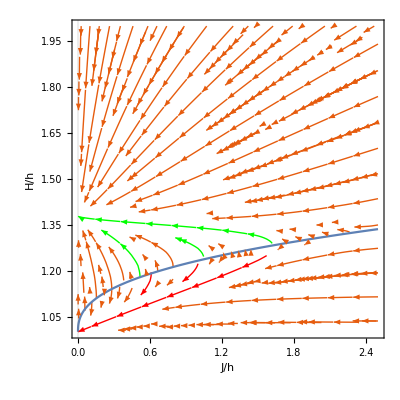

```mathematica
SFp1=StreamPlot[{dsj1[[2]]/.SFcase1,dsj2[[2]]/.SFcase1},{x[τ],0,2.5},{y[τ],1+10^-5,2},PlotTheme->{"Scientific","Red"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,15],FrameLabel->{Style["J/h",FontSize->16],Style["H/h",FontSize->16]},RotateLabel->False,PlotRange->{{0,2.5},{1,2}},StreamPoints->{{{{3/2,(z[τ]+1/.zSFcase1/.x[τ]->3/2)+(4 10^-2)},Green},{{1,(z[τ]+1/.zSFcase1/.x[τ]->1)+(4 10^-2)},Green},
{{1/2,(z[τ]+1/.zSFcase1/.x[τ]->1/2)+(4 10^-2)},Green},{{3/2,(z[τ]+1/.zSFcase1/.x[τ]->3/2)-(4 10^-2)},Red},{{1,(z[τ]+1/.zSFcase1/.x[τ]->1)-(1 10^-2)},Red},{{6/10,(z[τ]+1/.zSFcase1/.x[τ]->1/2)-(1 10^-2)},Red},Automatic},Fine}];
yc1=Plot[z[τ]+1/.zSFcase1/.x[τ]->x,{x,0,2.5}];
Show[SFp1,yc1]
```

We observe here an interesting case wherein aside from the expected de Sitter vacuum at H/h=1 there is also a de Sitter state at H/h=√λ. We can find this by checking out the y-axis...

```mathematica
Solve[{(Series[dsj2[[2]]/.n->1/.x[τ]->ϵ,{ϵ,0,0}]//Normal)==0,y[τ]>0,λ>0},y[τ]][[1]]
```

{y[τ]→ConditionalExpression[√λ,λ>0]}

Thus, the other de Sitter state corresponds to y=H/h=√λ, or in the earlier set of variables (Λ=3 h^2 λ), 3 H^2=Λ.

[Case 2: n=-2, λ=1.9,β=1,w=0]

Setting up...

```mathematica
SFcase2={n->-2,λ->7/5,β->1,w->0};
zSFcase2=Solve[{((dsj2[[2]]/.SFcase2//Denominator)/.y[τ]->z[τ]+1)==0},z[τ]][[2]]
(*"y_C(x)"==z[τ]+1/.zSFcase1/.x[τ]->x*)

noghostSF=-1/(λ-1)<n<0;noghostSF/.SFcase2
```

{z[τ]→x[τ]^(4/9)/(2^(1/9) 15^(5/9))}

True

The phase portraits of this dynamical system (figure 2) is shown below...

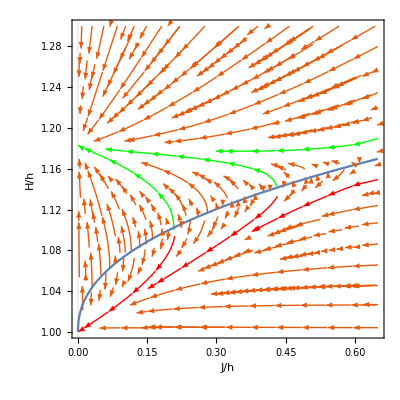

```mathematica
SFp2=StreamPlot[{dsj1[[2]]/.SFcase2,dsj2[[2]]/.SFcase2},{x[τ],0,0.65},{y[τ],1+10^-5,1.3},PlotTheme->{"Scientific","Red"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,15],FrameLabel->{Style["J/h",FontSize->16],Style["H/h",FontSize->16]},RotateLabel->False,PlotRange->{{0,0.65},{1,1.3}},StreamPoints->{{{{0.2,(z[τ]+1/.zSFcase2/.x[τ]->0.2)+(2 10^-2)},Green},{{0.4,(z[τ]+1/.zSFcase2/.x[τ]->0.4)+(2 10^-2)},Green},
{{0.6,(z[τ]+1/.zSFcase2/.x[τ]->0.6)+(2 10^-2)},Green},{{0.2,(z[τ]+1/.zSFcase2/.x[τ]->0.2)-(2 10^-2)},Red},{{0.4,(z[τ]+1/.zSFcase2/.x[τ]->0.4)-(2 10^-2)},Red},{{0.6,(z[τ]+1/.zSFcase2/.x[τ]->0.6)-(2 10^-2)},Red},Automatic},Fine}];
yc2=Plot[z[τ]+1/.zSFcase2/.x[τ]->x,{x,0,0.65}];
Show[SFp2,yc2]
```

#### 4.3(a) Multiple cosmic fluids

```mathematica
(*SetDirectory[NotebookDirectory[]];
Get["self_tuning_GCCG.m"]*)
```

In this section, we finally consider the more realistic case in which there is a nontrivial mixture of cosmic fluids. We add matter and vacuum-energy, with the abundances Ω_i=ρ_i a_0^(-3(1+w))/(3 H_0^2) where a_0 and H_0 are the present day scale factor and Hubble parameter, respectively,...

```mathematica
addmat={P->Function[t,P[t]+0 (ρm/a[t]^3)],ρ->Function[t,ρ[t]+(ρm/a[t]^3)]};
addrad={P->Function[t,P[t]+1/3 (ρr/a[t]^4)],ρ->Function[t,ρ[t]+(ρr/a[t]^4)]};
addvac={P->Function[t,P[t]-ρΛ],ρ->Function[t,ρ[t]+ρΛ]};

"ρ"==(ρ[t]/.addmat/.addrad/.addvac/.{ρ[t]->0,P[t]->0})
"ρ+P"==(ρ[t]+P[t]/.addmat/.addrad/.addvac/.{ρ[t]->0,P[t]->0})
```

ρ==ρΛ+ρr/a[t]^4+ρm/a[t]^3

ρ+P==(4 ρr)/(3 a[t]^4)+ρm/a[t]^3

The field equations become (Eqs. (4.24-26))...

```mathematica
$Assumptions=h≠0&&a[t]≠0&&ϕ'[t]≠0&&c≠0;
Feq1=(FeqGCCG/.addmat/.addrad/.addvac/.{ρ[t]->0,P[t]->0}/.H->Function[t,a'[t]/a[t]]//FullSimplify);
Heq1=(HeqGCCG/.addmat/.addrad/.addvac/.{ρ[t]->0,P[t]->0}/.H->Function[t,a'[t]/a[t]]//FullSimplify);
Seq1=(SeqGCCG/.addmat/.addrad/.addvac/.{ρ[t]->0,P[t]->0}/.H->Function[t,a'[t]/a[t]]//FullSimplify);

Feq1
Heq1
Seq1
```

2^n h (ρr+a[t] (ρm+ρΛ a[t]^3-3 a[t] a'[t]^2))+c a[t]^3 (h (-1+2 n) a[t]-2 n a'[t]) (ϕ'[t]^2)^n==0

2^n h ϕ'[t] (4 ρr+3 a[t] (ρm-2 a[t] a'[t]^2+2 a[t]^2 a''[t]))+2 c n a[t]^3 (ϕ'[t]^2)^n (3 (h a[t]-a'[t]) ϕ'[t]+a[t] ϕ''[t])==0

n ϕ'[t] (2 a'[t]^2+a[t] (-3 h a'[t]+a''[t]))==n (-1+2 n) a[t] (h a[t]-a'[t]) ϕ''[t]

We nondimensionalize the field equations. We set [c]=[T]^(2n-2) where [T] denotes a unit of time ([T]~h^-1). Using the coordinate τ=h t as a time variable, we obtain...

```mathematica
ctoβ=c->β h^(-(2n-2));
nondim={ϕ'[t]->h Ψ[τ],ϕ''[t]->h^2 Ψ'[τ],a[t]->a[τ],a'[t]->h a'[τ],a''[t]->h^2 a''[τ],ρm->3 h^2 αm,ρr->3 h^2 αr,ρΛ->3 h^2 αΛ};

Feq2=FullSimplify[Feq1/.ctoβ/.nondim,Assumptions->h>0&&n≠0];
Heq2=FullSimplify[Heq1/.ctoβ/.nondim,Assumptions->h>0&&n≠0];
Seq2=FullSimplify[Seq1/.ctoβ/.nondim,Assumptions->h>0&&n≠0];

Feq2
Heq2
Seq2
```

β a[τ]^3 (Ψ[τ]^2)^n ((-1+2 n) a[τ]-2 n a'[τ])+3 2^n (αr+a[τ] (αm+αΛ a[τ]^3-a[τ] a'[τ]^2))==0

2 n β a[τ]^3 (Ψ[τ]^2)^n (-3 Ψ[τ] a'[τ]+a[τ] (3 Ψ[τ]+Ψ'[τ]))+3 2^n Ψ[τ] (4 αr+3 αm a[τ]-2 a[τ]^2 a'[τ]^2+2 a[τ]^3 a''[τ])==0

h^3 n Ψ[τ] (2 a'[τ]^2+a[τ] (-3 a'[τ]+a''[τ]))==h^3 n (-1+2 n) a[τ] (a[τ]-a'[τ]) Ψ'[τ]

These are Eqs. (4.34-36). Integration proceeds by integrating the Hubble and scalar field equations subject to the Friedmann constraint. We recast the Hubble and scalar field equations as...

```mathematica
solaψ=Solve[{Heq2,Seq2},{a''[τ],Ψ'[τ]}][[1]]//Simplify;
ode1=a''[τ]-(a''[τ]/.solaψ)==0;
ode2=Ψ'[τ]-(Ψ'[τ]/.solaψ)==0;

ode1
ode2
```

(-2 n β a[τ]^3 (Ψ[τ]^2)^n (3 a[τ]-2 a'[τ]) a'[τ]+3 (-1+2 n) (a[τ]-a'[τ]) (2^(2+n) αr+3 2^n αm a[τ]+2 n β a[τ]^4 (Ψ[τ]^2)^n-2 n β a[τ]^3 (Ψ[τ]^2)^n a'[τ]-2^(1+n) a[τ]^2 a'[τ]^2))/(2 a[τ]^3 (n β a[τ] (Ψ[τ]^2)^n+3 2^n (-1+2 n) (a[τ]-a'[τ])))+a''[τ]==0

(3 Ψ[τ] (2^(2+n) αr+3 2^n αm a[τ]+2 n β a[τ]^4 (Ψ[τ]^2)^n+2 a[τ]^3 (3 2^n-n β (Ψ[τ]^2)^n) a'[τ]-3 2^(1+n) a[τ]^2 a'[τ]^2))/(2 a[τ]^3 (a[τ] (-3 2^n+3 2^(1+n) n+n β (Ψ[τ]^2)^n)-3 2^n (-1+2 n) a'[τ]))+Ψ'[τ]==0

Provided the four theory parameters {n,α_i} and the initial conditions {a(t_i),a'(t_i)}, ode1 and ode2 are ready for numerical integration. The initial condition Ψ(t_i) of the scalar field can be determined using the Friedmann constraint, F[a(t_i),a'(t_i),Ψ(t_i)].

Here is also the dark energy equation of state (Eq. (4.37))...

```mathematica
ρDEnd[τ_]=ρDEGCCG[t]/.ctoβ/.nondim/.H[t]->h H[τ]//Simplify;
PDEnd[τ_]=PDEGCCG[t]/.ctoβ/.nondim/.H[t]->h H[τ]//Simplify;

wDE[τ_]=PDEnd[τ]/ρDEnd[τ]//Simplify;

"w_DE"==wDE[τ]
```

w_DE==-(3 Ψ[τ]+2 n Ψ'[τ])/(3 Ψ[τ]-6 n Ψ[τ]+6 n H[τ] Ψ[τ])

...where H(τ)=a'(τ)/a(τ).

We compute the analytical expressions for the dark energy equations of state at the two attractors (in the variables of this section: H(τ)=1 and H(τ)=√α_Λ). We start with the unhealthy de Sitter state...

```mathematica
atoH=Solve[{H[τ]==a'[τ]/a[τ],D[H[τ]==a'[τ]/a[τ],τ]},{a'[τ],a''[τ]}][[1]];
dPsi=Solve[Seq2/.{αr->0,αm->0}/.atoH/.H->Function[τ,√αΛ]//Simplify,Ψ'[τ]][[1]];
"w_DE"==(wDE[τ]/.H->Function[τ,√αΛ]/.dPsi//Simplify)
```

w_DE==1/(-1+2 n)

For the self-tuning vacuum, we get...

```mathematica
Subscript[w, DE]==(wDE[τ]/.{H->Function[τ,1],Ψ->Function[τ,q]}//Simplify)
```

w_DE==-1

We’ll see these limits in action in the next section.

#### 4.3(b) Numerical experiments with multiple cosmic fluids

We investigate the self-tuning theories with n=-1,-2 explored in Sec. 4.2 with a nontrivial mixture of cosmic fluids with w=0 (dust) and w=1/3 (radiation).

Recall also the gradient stability constraint becomes -1/(k-1)<n<0 where α_Λ=k>1.

[Case 1: n=-1, λ=1.9,β=1]

Setting up the parameters...

```mathematica
param={β->1,n->-1};
abun={αr->1/10,αm->8/10,αΛ->19/10};

(*no-ghost condition*)
ngc=-1/(αΛ-1)<n<0;ngc/.abun/.param
n==(n/.param)
1/(Subscript[α, Λ]-1)==(1/(αΛ-1)/.abun/.param)
```

True

n==-1

1/(-1+α_Λ)==10/9

We consider a set of initial conditions that end up on the self-tuning de Sitter state...

```mathematica
(*initial conditions*)
ainit={ai->1,dai->6/5};
cons=NSolve[{Feq2/.param/.abun/.{a[τ]->ai,a'[τ]->dai,Ψ[τ]->dΨ}/.ainit,Re[dΨ]>0&&Im[dΨ]==0},dΨ,WorkingPrecision->50][[1]];
init=Union[ainit,cons];

a[Subscript[τ, 0]]==(ai/.init)
a'[Subscript[τ, 0]]==(dai/.init)
Ψ[Subscript[τ, 0]]==(dΨ/.init)
```

a[τ_0]==1

a'[τ_0]==6/5

Ψ[τ_0]==0.54232614454664043000013378128016430336745912051309

We integrate ode1 and ode2 using the following function...

```mathematica
cosmogccg[ai_,dai_,dΨ_,τ0_,τi_,τf_]:=NDSolve[{ode1/.abun/.param,ode2/.abun/.param,a[τ0]==ai,a'[τ0]==dai,Ψ[τ0]==dΨ},{a,Ψ},{τ,τi,τf},WorkingPrecision->50];
```

Testing this function for init...

```mathematica
dom={τ0->1,τi->1,τf->5};
int=cosmogccg[ai/.init,dai/.init,dΨ/.init,τ0/.dom,τi/.dom,τf/.dom];
```

Here is a plot of the solution.

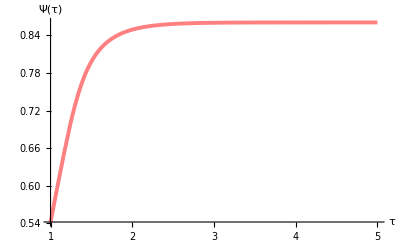

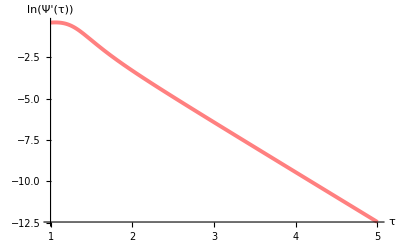

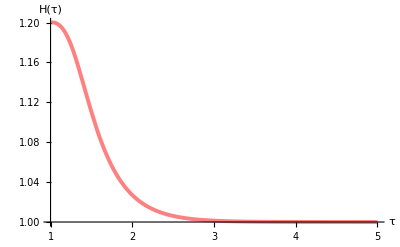

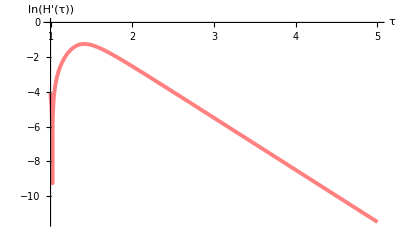

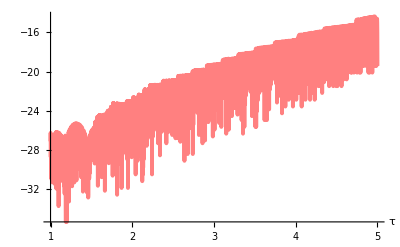

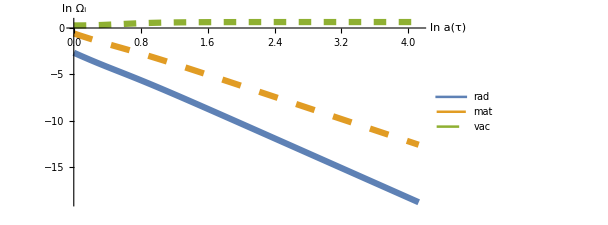

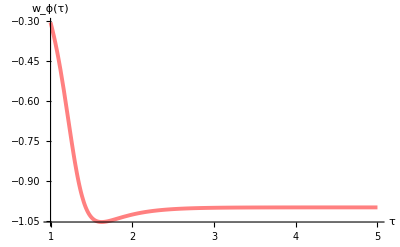

```mathematica
(*scalar field derivative*)
pΨ1=Plot[{Re[Ψ[τ]]/.int[[1]](*,Im[Ψ'[τ]]/.int[[1]]*)},{τ,τi,τf}/.dom,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","Ψ(τ)"}];

(*acceleration of scalar field*)
pdΨ1=Plot[{Re[Log[Ψ'[τ]]]/.int[[1]](*,Im[Ψ'[τ]]/.int[[1]]*)},{τ,τi,τf}/.dom,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ln(Ψ'(τ))"}];

(*Hubble parameter*)
pH1=Plot[{Re[a'[τ]/a[τ]]/.int[[1]]},{τ,τi,τf}/.dom,PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","H(τ)"}];

(*Hubble parameter time derivative*)
pdH1=Plot[{Log[Abs[Re[a''[τ]/a[τ]-(a'[τ]/a[τ])^2]]]/.int[[1]](*,Im[a''[τ]/a[τ]-(a'[τ]/a[τ])^2]/.int[[1]]*)},{τ,τi,τf}/.dom,PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ln(H'(τ))"}];

(*constraint equation*)
pF1=Plot[Log[Abs[Feq2[[1]]]/.param/.abun/.int[[1]]],{τ,τi,τf}/.dom,PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ",""}];

(*energy budget in units of h^2*)
(*Plot[{Log[(3 αr/a[τ]^4)(a[τ]^2/(3 a'[τ]^2))]/.abun/.int[[1]],Log[(3 αm/a[τ]^3)(a[τ]^2/(3 a'[τ]^2))]/.abun/.int[[1]],Log[(3αΛ)(a[τ]^2/(3 a'[τ]^2))]/.abun/.int[[1]](*,1-(3 αr/a[τ]^4+3 αm/a[τ]^3+3αΛ)a[τ]^2/(3 a'[τ]^2)/.abun/.int[[1]]*)},{τ,τi,τf}/.dom,PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007]},{Dashing[Large],Thickness[0.01]},{Dashing[Medium],Thickness[0.012]}},PlotLegends->{"rad","mat","vac"(*,"ϕ"*)},AxesLabel->{"τ","ln(Ω_i)"}]*)

(*log plot of energy budget*)
pbud1=ParametricPlot[{{Log[a[τ]]/.int[[1]],Log[(3 αr/a[τ]^4)(a[τ]^2/(3 a'[τ]^2))]/.abun/.int[[1]]},{Log[a[τ]]/.int[[1]],Log[(3 αm/a[τ]^3)(a[τ]^2/(3 a'[τ]^2))]/.abun/.int[[1]]},{Log[a[τ]]/.int[[1]],Log[(3αΛ)(a[τ]^2/(3 a'[τ]^2))]/.abun/.int[[1]]}},{τ,1,5},PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.01]},{Dashing[Large],Thickness[0.01]},{Dashing[Medium],Thickness[0.01]}},PlotLegends->{"rad","mat","vac","ϕ"},AspectRatio->1/2,AxesLabel->{"ln a(τ)","ln Ω_i"},ImageSize->450];

(*dark energy equation of state*)
pw1=Plot[wDE[τ]/.H[τ]->a'[τ]/a[τ]/.param/.int[[1]],{τ,τi,τf}/.dom,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","w_ϕ(τ)"}];

Show[pΨ1]
Show[pdΨ1]
Show[pH1]
Show[pdH1]
Show[pF1]
Show[pbud1]
Show[pw1]
```

We overlap the above results with another one with initial conditions ending up on the unhealthy late-time state...

```mathematica
(*initial conditions*)
ainit2={ai->100,dai->125};
cons2=NSolve[{Feq2/.param/.abun/.{a[τ]->ai,a'[τ]->dai,Ψ[τ]->dΨ}/.ainit2,Re[dΨ]>0&&Im[dΨ]==0},dΨ,WorkingPrecision->50][[1]];
init2=Union[ainit2,cons2];

a[Subscript[τ, 0]]==(ai/.init2)
a'[Subscript[τ, 0]]==(dai/.init2)
Ψ[Subscript[τ, 0]]==(dΨ/.init2)

int2=cosmogccg[ai/.init2,dai/.init2,dΨ/.init2,τ0/.dom,τi/.dom,τf/.dom];
```

a[τ_0]==100

a'[τ_0]==125

Ψ[τ_0]==0.99380681068319091518695224555467996499892431733603

Here are the overlaped plots.

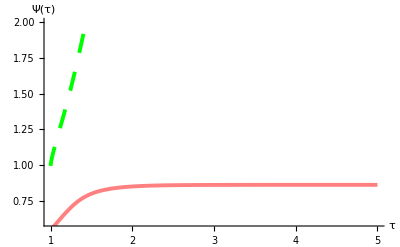

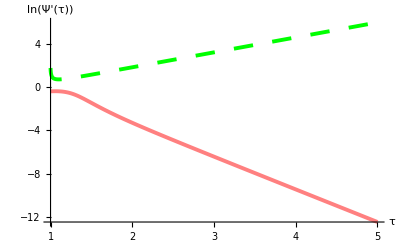

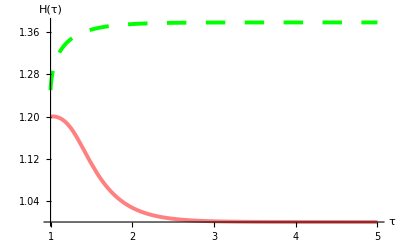

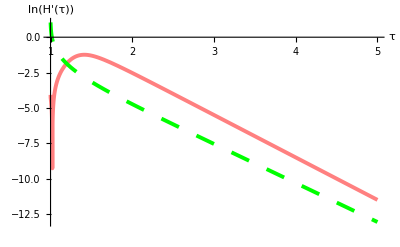

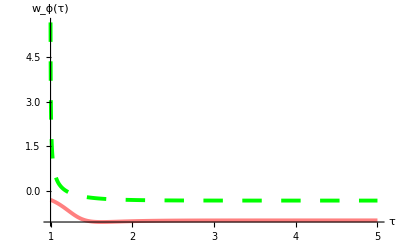

```mathematica
(*scalar field derivative*)
pΨ2=Plot[{Re[Ψ[τ]]/.int2[[1]](*,Im[Ψ'[τ]]/.int[[1]]*)},{τ,τi,τf}/.dom,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","Ψ(τ)"}];

(*acceleration of scalar field*)
pdΨ2=Plot[{Re[Log[Ψ'[τ]]]/.int2[[1]](*,Im[Ψ'[τ]]/.int[[1]]*)},{τ,τi,τf}/.dom,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","ln(Ψ'(τ))"}];

(*Hubble parameter*)
pH2=Plot[{Re[a'[τ]/a[τ]]/.int2[[1]]},{τ,τi,τf}/.dom,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","H(τ)"}];

(*Hubble parameter time derivative*)
pdH2=Plot[{Log[Abs[Re[a''[τ]/a[τ]-(a'[τ]/a[τ])^2]]]/.int2[[1]](*,Im[a''[τ]/a[τ]-(a'[τ]/a[τ])^2]/.int[[1]]*)},{τ,τi,τf}/.dom,PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","ln(H'(τ))"}];

(*dark energy equation of state*)
pw2=Plot[wDE[τ]/.H[τ]->a'[τ]/a[τ]/.param/.int2[[1]],{τ,τi,τf}/.dom,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","w_ϕ(τ)"}];

Show[pΨ1,pΨ2,PlotRange->{{1,5},{0.6,2}}]
Show[pdΨ1,pdΨ2,PlotRange->{{1,5},Automatic}]
Show[pH1,pH2,PlotRange->{{1,5},Automatic}]
Show[pdH1,pdH2,PlotRange->{{1,5},Automatic}]
Show[pw1,pw2,PlotRange->{{1,5},Automatic}]
```

The first four figures above are figure 3. The last one above and the figure below make figure 4.

We compare the vacuum energy densities in both cases as well...

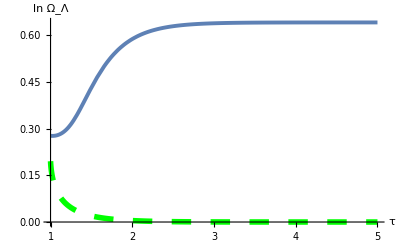

```mathematica
Plot[{Log[(3αΛ)(a[τ]^2/(3 a'[τ]^2))]/.abun/.int[[1]],Log[(3αΛ)(a[τ]^2/(3 a'[τ]^2))]/.abun/.int2[[1]]},{τ,τi,τf}/.dom,PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007]},{Dashing[Large],Thickness[0.01],Green}},AxesLabel->{"τ","ln Ω_Λ"}]
```

In the self-tuning vacuum (blue solid line) the late-time energy budget of the universe comes from a mixture of vacuum energy and the dark energy field. On the other hand, the unhealthy de Sitter state (green dashed line) is described by purely vacuum energy only, Ω_Λ=1.

[Case 2: n=-2, λ=7/5,β=1]

Setting up the theory...

```mathematica
(*theory parameters*)
param2={β->1,n->-2};
abun2={αr->1/10,αm->8/10,αΛ->7/5};

(*no-ghost condition*)
ngc=-1/(αΛ-1)<n<0;ngc/.abun2/.param2
n==(n/.param2)
1/(Subscript[α, Λ]-1)==(1/(αΛ-1)/.abun2/.param2)
```

True

n==-2

1/(-1+α_Λ)==5/2

We consider two initial conditions ending up on the two de Sitter limits...

```mathematica
(*initial conditions for self tuning vacuum*)
ainit3={ai->1,dai->11/10};
cons3=NSolve[{Feq2/.param2/.abun2/.{a[τ]->ai,a'[τ]->dai,Ψ[τ]->dΨ}/.ainit3,Re[dΨ]>0&&Im[dΨ]==0},dΨ,WorkingPrecision->50][[1]];
init3=Union[ainit3,cons3];

ainit4={ai->100,dai->112};
cons4=NSolve[{Feq2/.param2/.abun2/.{a[τ]->ai,a'[τ]->dai,Ψ[τ]->dΨ}/.ainit4,Re[dΨ]>0&&Im[dΨ]==0},dΨ,WorkingPrecision->50][[1]];
init4=Union[ainit4,cons4];
```

Preparing the integration with this function...

```mathematica
cosmogccg2[ai_,dai_,dΨ_,τ0_,τi_,τf_]:=NDSolve[{ode1/.abun2/.param2,ode2/.abun2/.param2,a[τ0]==ai,a'[τ0]==dai,Ψ[τ0]==dΨ},{a,Ψ},{τ,τi,τf},WorkingPrecision->50];
```

Integrating the field equations...

```mathematica
dom2={τ0->1,τi->1,τf->5};
int3=cosmogccg2[ai/.init3,dai/.init3,dΨ/.init3,τ0/.dom2,τi/.dom2,τf/.dom2];
int4=cosmogccg2[ai/.init4,dai/.init4,dΨ/.init4,τ0/.dom2,τi/.dom2,τf/.dom2];
```

Plotting the results...

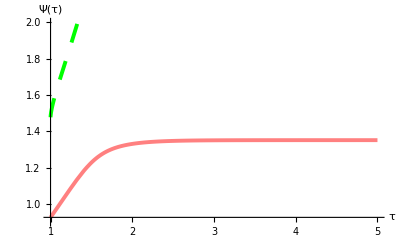

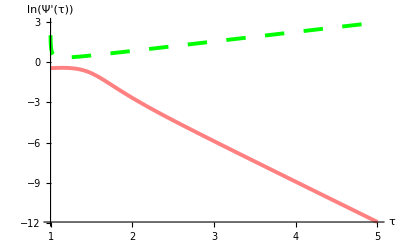

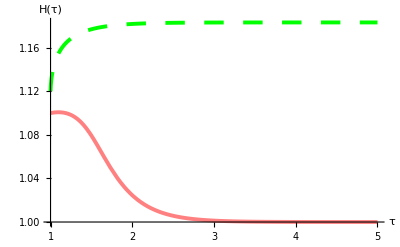

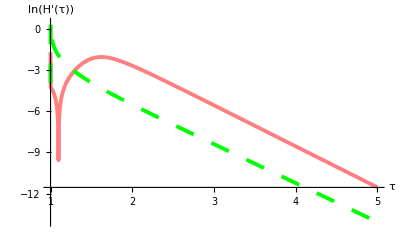

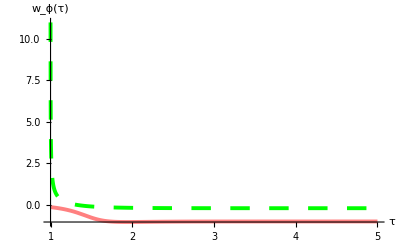

```mathematica
(*scalar field derivative*)
pΨ3=Plot[{Re[Ψ[τ]]/.int3[[1]](*,Im[Ψ'[τ]]/.int[[1]]*)},{τ,τi,τf}/.dom2,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","Ψ(τ)"}];
pΨ4=Plot[{Re[Ψ[τ]]/.int4[[1]](*,Im[Ψ'[τ]]/.int[[1]]*)},{τ,τi,τf}/.dom2,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","Ψ(τ)"}];

(*acceleration of scalar field*)
pdΨ3=Plot[{Re[Log[Ψ'[τ]]]/.int3[[1]](*,Im[Ψ'[τ]]/.int[[1]]*)},{τ,τi,τf}/.dom2,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ln(Ψ'(τ))"}];
pdΨ4=Plot[{Re[Log[Ψ'[τ]]]/.int4[[1]](*,Im[Ψ'[τ]]/.int[[1]]*)},{τ,τi,τf}/.dom2,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","ln(Ψ'(τ))"}];

(*Hubble parameter*)
pH3=Plot[{Re[a'[τ]/a[τ]]/.int3[[1]]},{τ,τi,τf}/.dom2,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","H(τ)"}];
pH4=Plot[{Re[a'[τ]/a[τ]]/.int4[[1]]},{τ,τi,τf}/.dom2,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","H(τ)"}];

(*Hubble parameter time derivative*)
pdH3=Plot[{Log[Abs[Re[a''[τ]/a[τ]-(a'[τ]/a[τ])^2]]]/.int3[[1]](*,Im[a''[τ]/a[τ]-(a'[τ]/a[τ])^2]/.int[[1]]*)},{τ,τi,τf}/.dom2,PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ln(H'(τ))"}];
pdH4=Plot[{Log[Abs[Re[a''[τ]/a[τ]-(a'[τ]/a[τ])^2]]]/.int4[[1]](*,Im[a''[τ]/a[τ]-(a'[τ]/a[τ])^2]/.int[[1]]*)},{τ,τi,τf}/.dom2,PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","ln(H'(τ))"}];

(*dark energy equation of state*)
pw3=Plot[wDE[τ]/.H[τ]->a'[τ]/a[τ]/.param2/.int3[[1]],{τ,τi,τf}/.dom,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","w_ϕ(τ)"}];
pw4=Plot[wDE[τ]/.H[τ]->a'[τ]/a[τ]/.param2/.int4[[1]],{τ,τi,τf}/.dom,PlotRange->All,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[Large],Thickness[0.007],Green}},AxesLabel->{"τ","w_ϕ(τ)"}];

Show[pΨ3,pΨ4,PlotRange->{{1,5},{0.9,2}}]
Show[pdΨ3,pdΨ4,PlotRange->{{1,5},Automatic}]
Show[pH3,pH4,PlotRange->{{1,5},Automatic}]
Show[pdH3,pdH4,PlotRange->{{1,5},Automatic}]
Show[pw3,pw4,PlotRange->{{1,5},Automatic}]
```

Comparing the vacuum energies in both de Sitter states...

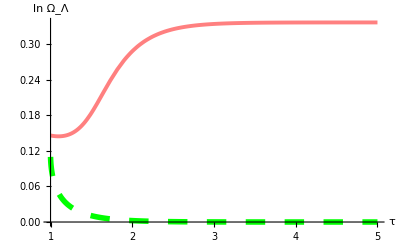

```mathematica
Plot[{Log[(3αΛ)(a[τ]^2/(3 a'[τ]^2))]/.abun2/.int3[[1]],Log[(3αΛ)(a[τ]^2/(3 a'[τ]^2))]/.abun2/.int4[[1]]},{τ,τi,τf}/.dom2,PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink},{Dashing[Large],Thickness[0.01],Green}},AxesLabel->{"τ","ln Ω_Λ"}]
```

These are figures 5 and 6 in the text.

#### 4.4 Phase transitions

```mathematica
(*SetDirectory[NotebookDirectory[]];
Get["self_tuning_GCCG.m"]*)
```

In this section, we show that the self-tuning vacuum of tadpole-free shift symmetric KGB can survive phase transitions.

We implement this using the following effective source...

```mathematica
ptρ=ρ->Function[t,Λ+(ΔΛ/2 Tanh[(t-T)/Δt])];
ptP=P->Function[t,-ρ[t]-ρ'[t]/(3H[t])];
```

...where Λ is an initial cosmological constant that would be changed by ΔΛ in a short time interval Δt at a time T. Here is a plot of the effective energy density and pressure (figure 7)...

(ρ_eff(τ))/(3 h^2)==λ+1/2 Δλ Tanh[(τ-Τ)/Δτ]

(P_eff(τ))/(3 h^2)==-λ-(Δλ Sech[(τ-Τ)/Δτ]^2)/(6 Δτ)-1/2 Δλ Tanh[(τ-Τ)/Δτ]

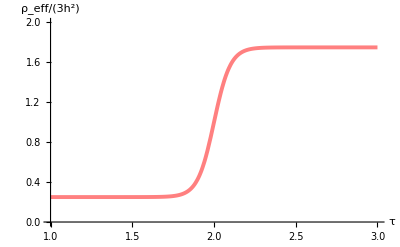

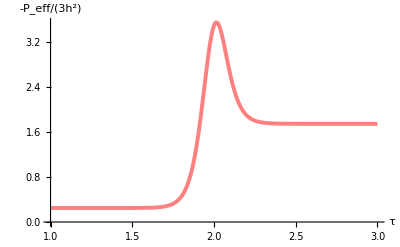

```mathematica
ρnd[τ_]=(ρ[t]/.ptρ/.{t->h τ,T->h Τ,Δt->h Δτ,Λ->3 h^2 λ,ΔΛ->3 h^2 Δλ}//Simplify);
Pnd[τ_]=(P[t]/.ptP/.ptρ/.H[t]->h/.{t->h τ,T->h Τ,Δt->h Δτ,Λ->3 h^2 λ,ΔΛ->3 h^2 Δλ}//Simplify);

"(ρ_eff(τ))/(3 h^2)"==ρnd[τ]/(3 h^2)//Expand
"(P_eff(τ))/(3 h^2)"==Pnd[τ]/(3 h^2)/.h->1//Expand

Plot[{ρnd[τ]/(3 h^2)/.{λ->1,Δλ->3/2,Τ->2,Δτ->1/10}},{τ,1,3},PlotRange->{{1,3},{0,2}},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ρ_eff/(3h^2)"}]

Plot[{-Pnd[τ]/(3 h^2)/.h->1/.{λ->1,Δλ->3/2,Τ->2,Δτ->1/10}},{τ,1,3},PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","-P_eff/(3h^2)"},AxesOrigin->{1,0}]
```

We now setup the field equations. We proceed by eliminating the energy density in the Friedmann constraint and Hubble equation and substitute the effective pressure...

```mathematica
FHeq=HeqGCCG/.Solve[FeqGCCG,ρ[t]][[1]]/.ptP/.ptρ//Simplify;FHeq
```

9 2^n H[t]^2+3 2^(1+n) H'[t]+(c (ϕ'[t]^2)^n (3 h ϕ'[t]+2 n ϕ''[t]))/(h ϕ'[t])==(2^(-1+n) (ΔΛ Sech[(t-T)/Δt]^2+3 Δt H[t] (2 Λ+ΔΛ Tanh[(t-T)/Δt])))/(Δt H[t])

The dynamical system is given by...

```mathematica
ds=Solve[{FHeq,SeqGCCG},{ϕ''[t],H'[t]}][[1]]//Simplify;

ds1=ϕ''[t]==(ϕ''[t]/.ds);
ds2=H'[t]==(H'[t]/.ds);

ds1
ds2
```

ϕ''[t]==-((h ϕ'[t] (9 2^(2+n) h Δt H[t]^2-9 2^(1+n) Δt H[t]^3-2^n ΔΛ Sech[(t-T)/Δt]^2-3 Δt H[t] (2^(1+n) Λ+2^n ΔΛ Tanh[(t-T)/Δt]-2 c (ϕ'[t]^2)^n)))/(4 Δt H[t] (3 2^n h^2 (-1+2 n)-3 2^n h (-1+2 n) H[t]+c n (ϕ'[t]^2)^n)))

H'[t]==-(((h-H[t]) (9 2^(1+n) h (-1+2 n) Δt H[t]^3-2^n h (-1+2 n) ΔΛ Sech[(t-T)/Δt]^2-12 c n Δt H[t]^2 (ϕ'[t]^2)^n-3 h (-1+2 n) Δt H[t] (2^(1+n) Λ+2^n ΔΛ Tanh[(t-T)/Δt]-2 c (ϕ'[t]^2)^n)))/(4 Δt H[t] (3 2^n h^2 (-1+2 n)-3 2^n h (-1+2 n) H[t]+c n (ϕ'[t]^2)^n)))

Nondimensionalizing leads to Eqs. (4.48) and (4.49)...

```mathematica
ctoβ=c->β h^(-(2n-2));
nondim={ϕ'[t]->h Ψ[τ],ϕ''[t]->h^2 Ψ'[τ],H[t]->h y[τ],H'[t]->h^2 y'[τ],Λ->3 h^2 λ,ΔΛ->3 h^2 Δλ};
nondim2={t->h τ,T->h Τ,Δt->h Δτ};

ds1nd=(ds1[[1]]/.nondim)==(FullSimplify[ds1[[2]]/.ctoβ/.nondim/.nondim2,Element[n,Reals]&&Element[β,Reals]&&Element[h,Reals],Assumptions->β>0&&h>0]);
ds2nd=(ds2[[1]]/.nondim)==FullSimplify[ds2[[2]]/.ctoβ/.nondim/.nondim2,Element[n,Reals]&&Element[β,Reals]&&Element[h,Reals],Assumptions->β>0&&h>0];

ds1nd
ds2nd
```

h^2 Ψ'[τ]==(-3 2^n (Δλ Sech[(τ-Τ)/Δτ]^2+3 h^2 Δτ y[τ] (2 λ+Δλ Tanh[(τ-Τ)/Δτ]+2 (-2+y[τ]) y[τ])) Ψ[τ]+6 h^2 β Δτ y[τ] Ψ[τ] (Ψ[τ]^2)^n)/(4 Δτ y[τ] (3 2^n (-1+2 n) (-1+y[τ])-n β (Ψ[τ]^2)^n))

h^2 y'[τ]==(3 (-1+y[τ]) (2^n (-1+2 n) (Δλ Sech[(τ-Τ)/Δτ]^2+3 h^2 Δτ y[τ] (2 λ+Δλ Tanh[(τ-Τ)/Δτ]-2 y[τ]^2))+2 h^2 β Δτ y[τ] (1-2 n+2 n y[τ]) (Ψ[τ]^2)^n))/(4 Δτ y[τ] (3 2^n (-1+2 n) (-1+y[τ])-n β (Ψ[τ]^2)^n))

There is an unaccounted units in the term P~-ρ'/(3 H^2) that amounts to h^2. Overall both sides of both equations will have h^2 and so we set h=1...

```mathematica
ds1ND=ds1nd/.h->1;
ds2ND=ds2nd/.h->1;

ds1ND
ds2ND
```

Ψ'[τ]==(-3 2^n (Δλ Sech[(τ-Τ)/Δτ]^2+3 Δτ y[τ] (2 λ+Δλ Tanh[(τ-Τ)/Δτ]+2 (-2+y[τ]) y[τ])) Ψ[τ]+6 β Δτ y[τ] Ψ[τ] (Ψ[τ]^2)^n)/(4 Δτ y[τ] (3 2^n (-1+2 n) (-1+y[τ])-n β (Ψ[τ]^2)^n))

y'[τ]==(3 (-1+y[τ]) (2^n (-1+2 n) (Δλ Sech[(τ-Τ)/Δτ]^2+3 Δτ y[τ] (2 λ+Δλ Tanh[(τ-Τ)/Δτ]-2 y[τ]^2))+2 β Δτ y[τ] (1-2 n+2 n y[τ]) (Ψ[τ]^2)^n))/(4 Δτ y[τ] (3 2^n (-1+2 n) (-1+y[τ])-n β (Ψ[τ]^2)^n))

We note the choice of α and Δα should still respect the gradient stability constraint: n>-1/(α_i-1).

[n=-1]

Setting up the parameters and the integration function...

```mathematica
case1={n->-1,β->1};
(*choice is so that Subscript[λ, i]=19/10 corresponding to previous cases*)
ptparam1={λ->33/20,Δλ->-1/2,Δτ->1/10,Τ->2};

ng1=n>-1/((λ-Δλ/2)-1);ng1/.case1/.ptparam1
ng2=n>-1/((λ+Δλ/2)-1);ng2/.case1/.ptparam1

PTint[Ψ0_,y0_,τ0_,τf_]:=NDSolve[{ds1ND/.case1/.ptparam1,ds2ND/.case1/.ptparam1,Ψ[τ0]==Ψ0,y[τ0]==y0},{Ψ,y},{τ,τ0,τf},WorkingPrecision->50]
```

True

True

...we obtain...

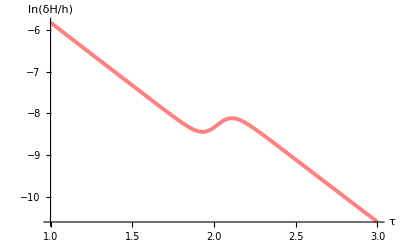

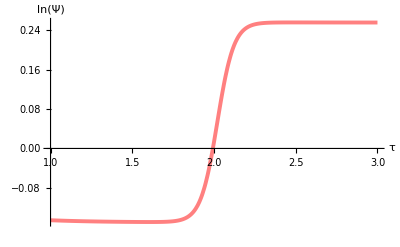

```mathematica
PT1=PTint[1,11/10,0,5][[1]];

Plot[{Log[y[τ]-1]/.PT1},{τ,1,3},PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ln(δH/h)"}]

Plot[{Log[Ψ[τ]]/.PT1},{τ,1,3},PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ln(Ψ)"}]
```

We can also just easily match the asymptotic solutions obtained in Sec. IIIC, namely, δH~e^(-3h t)=e^(-3τ). We input this asymptotic expression as follows and find its coefficient manually...

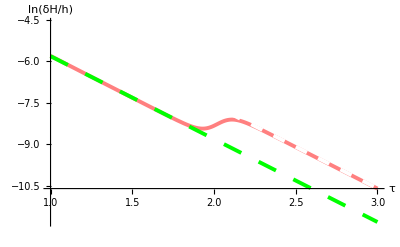

```mathematica
approx[x_,dash_,thick_,color_]:=Plot[Log[x E^(-3τ)],{τ,1,3},PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Dashing[dash],Thickness[thick],color}}];

pt1h=Plot[{Log[y[τ]-1]/.PT1},{τ,1,3},PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ln(δH/h)"}];

Show[pt1h,approx[E^-2.82,Large,0.007,Green],approx[E^-1.6,Medium,0.007,White],PlotRange->All]
```

The three plots above make figure 8. Clearly, the asymptotic solutions hold in both phases.

[n=-2]

Setting up the parameters and the integration function...

```mathematica
case2={n->-2,β->1};
(*chosen so that Subscript[λ, i]=7/5 corresponding to previous cases*)
ptparam2={λ->51/40,Δλ->-1/4,Δτ->1/10,Τ->2};

ng1=n>-1/((λ-Δλ/2)-1);ng1/.case2/.ptparam2
ng2=n>-1/((λ+Δλ/2)-1);ng2/.case2/.ptparam2

PTint2[Ψ0_,y0_,τ0_,τf_]:=NDSolve[{ds1ND/.case2/.ptparam2,ds2ND/.case2/.ptparam2,Ψ[τ0]==Ψ0,y[τ0]==y0},{Ψ,y},{τ,τ0,τf},WorkingPrecision->50]
```

True

True

...we obtain the results...

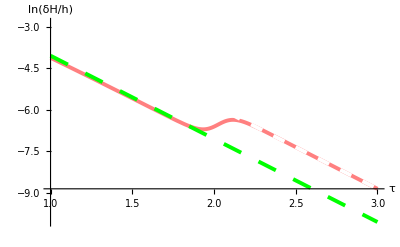

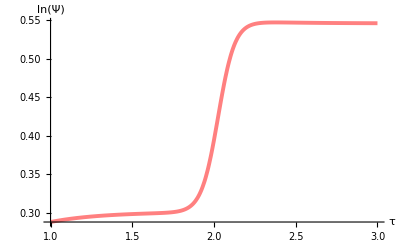

```mathematica
PT2=PTint2[1,12/11,0,5][[1]];

pt2h=Plot[{Log[y[τ]-1]/.PT2},{τ,1,3},PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ln(δH/h)"}];

Show[pt2h,approx[E^-1.05,Large,0.007,Green],approx[E^0.15,Medium,0.007,White],PlotRange->All]

Plot[{Log[Ψ[τ]]/.PT2},{τ,1,3},PlotRange->Automatic,AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","ln(Ψ)"}]
```

The above plots make figure 9.

### Section 5. Self-tuning exponential KGB

We check out cosmological dynamics in the exponential KGB. Importing the results of Sec. 3...

```mathematica
(*SetDirectory[NotebookDirectory[]];
Get["trivial_scalar_field_eqs.m"]*)
```

The field equations are given by...

```mathematica
ExpKGB={l->0,A->Function[x,c E^(x/d)]};

"A(X)"==A[X]/.ExpKGB
"B(x)"==∫(B'[X]/.stmod/.ExpKGB//Simplify)ⅆX

FeqExpKGB=FeqTPST/.ExpKGB//FullSimplify;
HeqExpKGB=HeqTPST/.ExpKGB//FullSimplify;
SeqExpKGB=SeqTPST/.ExpKGB//FullSimplify;

FE2ExpKGB=FE2TPST/.ExpKGB//FullSimplify;

FeqExpKGB
HeqExpKGB
SeqExpKGB
```

A(X)==c ⅇ^(X/d)

B(x)==-(c √π Erfi[(√X)/(√d)])/(3 √2 √d h)

(d h (3 H[t]^2-ρ[t])+c ⅇ^(ϕ'[t]^2/(2 d)) (d h+(-h+H[t]) ϕ'[t]^2))/(d h)==0

P[t]+ρ[t]+2 H'[t]+(c ⅇ^(ϕ'[t]^2/(2 d)) ϕ'[t] (3 (h-H[t]) ϕ'[t]+ϕ''[t]))/(3 d h)==0

1/(d h)c ⅇ^(ϕ'[t]^2/(2 d)) (d (3 (h-H[t]) H[t]-H'[t]) ϕ'[t]+(h-H[t]) (d+ϕ'[t]^2) ϕ''[t])==0

The gradient stability constraint on the de Sitter vacuum becomes...

```mathematica
ggstab/.ExpKGB
```

-(3 h^2)/X<(c ⅇ^(X/d))/d<0

Noting c>0 because of the Hamiltonian constraint and Λ≫3 h^2...

```mathematica
FeqExpKGB/.{H[t]->h,ρ[t]->Λ}/.ϕ'[t]->√(2X)//Simplify
```

c ⅇ^(X/d)+3 h^2==Λ

...we find the gradient condition implies d<0. With this, we see that the constant c must scale as Λ in order to counterbalance its effect on the de Sitter state. Also, unlike the previous case of the generalized cubic covariant Galileon, we find that the gradient constraint do not prevent the theory from tuning away an arbitrarily large vacuum energy. We show this explicitly by nondimensionalizing the gradient constraint and the Hamiltonian constraint...

```mathematica
$Assumptions=γ>0&&Γ<0&&h>0&&χ>0;
ndExpKGB={Λ->r(3 h^2),c->γ(3 h^2),d->Γ(3 h^2),X->χ(3 h^2)};

ggstabExpKGB=ggstab/.ExpKGB/.ndExpKGB;
FeqExpKGBnd=FeqExpKGB/.{H[t]->h,ρ[t]->Λ}/.ϕ'[t]->√(2X)/.ndExpKGB//Simplify;

ggstabExpKGB
FeqExpKGBnd
```

-1/χ<(ⅇ^(χ/Γ) γ)/Γ<0

r==1+ⅇ^(χ/Γ) γ

The second part of the inequality (A_X<0) is already satisfied. We focus on the first part, eliminating χ from the Friedmann constraint and using the substitution ζ=e^(χ/Γ),...

```mathematica
ggExpKGB=ggstabExpKGB[[1]]<ggstabExpKGB[[2]]/.E^(χ/Γ)->ζ/.χ->Γ Log[ζ]/.Solve[FeqExpKGBnd/.E^(χ/Γ)->ζ,γ][[1]]//Simplify;

ggExpKGB
```

Log[ζ] (1+(-1+r) Log[ζ])<0

Noting χ/Γ<0 since Γ<0 and χ>0, then ζ<1 and ln(ζ)<0, the above inequality becomes 1+(r-1)ln(ζ)>0 which is Eq. (5.7). For 0<ζ<1 and r=Λ/(3 h^2)≫1, this is satisfied.

We end this section by setting up the dynamical system for this theory provided a single non-Λ cosmic fluid...

```mathematica
FHeqSFExpKGB=HeqExpKGB/.ρ[t]->-P[t]+(1+w)ρ[t]/.Solve[FeqExpKGB/.ρ[t]->ρ[t]+Λ,ρ[t]][[1]]//Simplify;

FHeqSFExpKGB
```

2 H'[t]+(1+w) (-Λ+3 H[t]^2+(c ⅇ^(ϕ'[t]^2/(2 d)) (d h+(-h+H[t]) ϕ'[t]^2))/(d h))+(c ⅇ^(ϕ'[t]^2/(2 d)) ϕ'[t] (3 (h-H[t]) ϕ'[t]+ϕ''[t]))/(3 d h)==0

However, instead of replacing the scalar field ϕ with the shift current J, we retain the use of ϕ to avoid dealing with subtleties of the Lambert W function (or ProductLog), i.e.,...

```mathematica
ϕToJExpKGB=Solve[J[t]==Jst[t]/.ExpKGB,ϕ'[t]][[1]];

ϕToJExpKGB
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ϕ'[t]→-√d √ProductLog[(d h^2 J[t]^2)/(c^2 (h-H[t])^2)]}

The dynamical system is therefore...

```mathematica
dsExpKGB=Solve[{FHeqSFExpKGB,SeqExpKGB},{H'[t],ϕ''[t]}][[1]]//Simplify;

dsExpKGB1=ϕ''[t]==(ϕ''[t]/.dsExpKGB//FullSimplify);
dsExpKGB2=H'[t]==(H'[t]/.dsExpKGB//FullSimplify);

dsExpKGB1
dsExpKGB2
```

ϕ''[t]==(3 ϕ'[t] (d h ((1+w) Λ-6 h H[t]-3 (-1+w) H[t]^2)-c ⅇ^(ϕ'[t]^2/(2 d)) (d h (1+w)+w (-h+H[t]) ϕ'[t]^2)))/(c ⅇ^(ϕ'[t]^2/(2 d)) ϕ'[t]^2+6 h (h-H[t]) (d+ϕ'[t]^2))

H'[t]==(3 (h-H[t]) (d h (1+w) (Λ-3 H[t]^2) (d+ϕ'[t]^2)-c ⅇ^(ϕ'[t]^2/(2 d)) (d^2 h (1+w)+d (h+(-1+w) H[t]) ϕ'[t]^2+w (-h+H[t]) ϕ'[t]^4)))/(c d ⅇ^(ϕ'[t]^2/(2 d)) ϕ'[t]^2+6 d h (h-H[t]) (d+ϕ'[t]^2))

Nondimensionalizing using the length scale h^-1, we get...

```mathematica
ndExpKGBds={ϕ'[t]->h x[τ],ϕ''[t]->h^2 x'[τ],H[t]->h y[τ],H'[t]->h^2 y'[τ],Λ->λ(3 h^2),c->γ(3 h^2),d->Γ(3 h^2)};

dsExpKGBxy=Solve[{dsExpKGB1/.ndExpKGBds//Simplify,dsExpKGB2/.ndExpKGBds//Simplify},{x'[τ],y'[τ]}][[1]];

dsExpKGB1nd=x'[τ]==(x'[τ]/.dsExpKGBxy//FullSimplify);
dsExpKGB2nd=y'[τ]==(y'[τ]/.dsExpKGBxy//FullSimplify);

dsExpKGB1nd
dsExpKGB2nd
```

x'[τ]==(3 x[τ] (ⅇ^(x[τ]^2/(6 Γ)) γ (3 (1+w) Γ+w x[τ]^2 (-1+y[τ]))+3 Γ (-(1+w) λ+y[τ] (2+(-1+w) y[τ]))))/(-ⅇ^(x[τ]^2/(6 Γ)) γ x[τ]^2+2 (3 Γ+x[τ]^2) (-1+y[τ]))

y'[τ]==((-1+y[τ]) (3 (1+w) Γ (3 Γ+x[τ]^2) (λ-y[τ]^2)-ⅇ^(x[τ]^2/(6 Γ)) γ (9 (1+w) Γ^2+w x[τ]^4 (-1+y[τ])+3 Γ x[τ]^2 (1+(-1+w) y[τ]))))/(-ⅇ^(x[τ]^2/(6 Γ)) γ Γ x[τ]^2+2 Γ (3 Γ+x[τ]^2) (-1+y[τ]))

The fixed points at the self-tuning vacuum, y=1, can be found easily...

```mathematica
dsExpKGB1nd/.y[τ]->1//Simplify
dsExpKGB2nd/.y[τ]->1//Simplify
```

x'[τ]==-(9 ⅇ^(-x[τ]^2/(6 Γ)) (1+w) Γ (1+ⅇ^(x[τ]^2/(6 Γ)) γ-λ))/(γ x[τ])

y'[τ]==0

The fixed point on the positive x axis is given by...

```mathematica
xdsExpKGB=Solve[(dsExpKGB1nd[[2]]/.y[τ]->1//Simplify)==0,x[τ]][[2]]//Quiet;

"x"==(x[τ]/.xdsExpKGB)
```

x==√Γ √Log[(-1+λ)^6/γ^6]

Given Γ<0 (gradient constraint), we take in mind that this will be only for...

```mathematica
xdsExpKGBreal=(λ-1)/γ<1;xdsExpKGBreal
```

(-1+λ)/γ<1

The fixed point with y^2=λ can be similarly found. This will be at x→∞. We also note about a fixed point at x=0 with y given by...

```mathematica
y0fpExpKGB=Solve[(dsExpKGB2nd[[2]]/.x[τ]->0//Simplify)==0,y[τ]][[2]];

"y"==(y[τ]/.y0fpExpKGB)
```

y==√(-γ+λ)

Note this will be real for λ>γ but is compatible with the previous inequality λ-1<γ only in the narrow inequality λ-1<γ<λ. Also note the critical curve partitioning the phase space...

```mathematica
CritCExpKGB=DSolve[(dsExpKGB1nd[[2]]//Denominator)==0,y,τ][[1]];

"y(x)"==(y[τ]/.CritCExpKGB/.x[τ]->x)

(*define GetyOnC*)
GetyOnC[z_]:=(y[τ]/.CritCExpKGB/.x[τ]->z)
```

y(x)==(2 x^2+ⅇ^(x^2/(6 Γ)) x^2 γ+6 Γ)/(2 (x^2+3 Γ))

Let us checkout the phase portrait of the system...

True

True

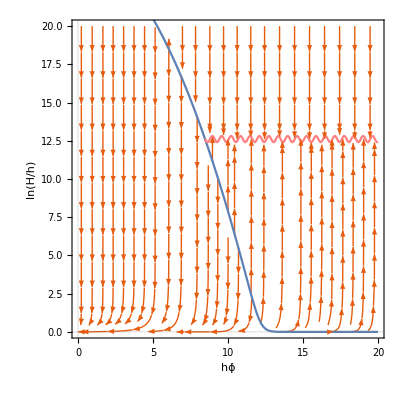

```mathematica
SFCase1ExpKGB={w->0,λ->9 10^10,γ->9 10^10-1/2,Γ->-1};

(*checks: x real, gradient stability*)
xdsExpKGBreal/.SFCase1ExpKGB
ggstabExpKGB/.SFCase1ExpKGB/.NSolve[FeqExpKGBnd/.r->λ/.SFCase1ExpKGB,χ,Reals][[1]]

SFp1ExpKGB=StreamPlot[{dsExpKGB1nd[[2]]/.SFCase1ExpKGB/.y->Function[a,E^y[a]],dsExpKGB2nd[[2]]/.SFCase1ExpKGB/.y->Function[a,E^y[a]]},{x[τ],0,20},{y[τ],10^-5,20},PlotTheme->{"Scientific","Red"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,15],FrameLabel->{Style["hϕ̇",FontSize->16],Style["ln(H/h)",FontSize->16]},RotateLabel->False,PlotRange->{{0,20},{0,20}}];

yc1ExpKGB=Plot[Log[y[τ]]/.CritCExpKGB/.x[τ]->x/.SFCase1ExpKGB,{x,0,20}];

xλ0ExpKGB=NSolve[y==(y[τ]/.CritCExpKGB/.x[τ]->x)/.y->√λ/.SFCase1ExpKGB,x,Reals][[2]];
yλ01ExpKGB=Plot[Log[√λ]+Sin[10x]/5/.SFCase1ExpKGB,{x,(x/.xλ0ExpKGB),20},PlotStyle->Pink];

Show[SFp1ExpKGB,yc1ExpKGB,yλ01ExpKGB]
```

This is figure 10(a).